## Dressed black holes in the new tensor-vector-scalar theory

Author: Reggie Bernardo (reginaldchristianbernardo@gmail.com)

This is a supplement to arXiv:xxxx.xxxxx. We derive hairy black hole solutions in the new tensor-vector-scalar theory (2007.00082). We acknowledge the xAct, xPert, and xCoba packages for tensor manipulation and calculus.

*To go straight into the black hole solutions, one may skip Secs. 0, I, and II if feqs_isotropic_coords.m is already available. For a full derivation starting from the Lagrangian, Secs. 0, I, and II may be run. The entire code takes around ~10-20 minutes to run.

### 0 Setup

Starting points, define manifold, constants, fields...

```mathematica
<<xAct`xPert`;
<<xAct`xCoba`;

(* aesthetics *)
$CovDFormat="Prefix";
$DefInfoQ=False;
$CVVerbose=False;

(* define manifold and metric *)
dim=4;    
DefManifold[Md,dim,{b,c,d,e,f,i,j,k}];
DefMetric[-1,g[-b,-c],CD,{";","∇"},WeightedWithBasis->AIndex];
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
PrintAs[Detg]^="g";

(* define scalar field and potentials *)
DefTensor[ϕ[],Md];
DefScalarFunction[ℱ];
DefConstantSymbol/@{κ,Κ}

(* define vector field *)
DefTensor[A[-b],Md];
DefTensor[F[-b,-c],Md,Antisymmetric[{-b,-c}]];
IndexSetDelayed[F[b_,c_],CD[b][A[c]]-CD[c][A[b]]];

(* for the collective matter *)
DefScalarFunction/@{ρ,P};
DefTensor[J[b],Md];
DefTensor[u[b],Md];
DefTensor[l[],Md];
DefTensor[n[],Md];

(* aesthetics: to remove red scalar parenthesis *)
UnRed=Scalar[expr_]:>expr;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

{Null,Null}

CP code for variational differentiation in xTensor (see ActionVariation_Metric_Fields.nb in the xAct examples repository)...

```mathematica
PerturbAction[expr_,g_?MetricQ[a_?UpIndexQ,b_?UpIndexQ]|g_?MetricQ[a_?DownIndexQ,b_?DownIndexQ]]:=Module[{pertexpr,res,dgloc,(*dummyloc,*)hp},

(* We define the metric perturbation, if not defined already *)
dgloc=SymbolJoin["δ",g];

hp=Head@Perturbation[g[DownIndex@a,DownIndex@b]];

If[hp===Perturbation,DefMetricPerturbation[g,dgloc,SymbolJoin["ϵ",g]],dgloc=hp];


Block[{$DefInfoQ=False},

(* We perturb wrt to the metric and if it is the inverse metric we put a minus sign *)
pertexpr=(If[DownIndexQ[a],1,-1])*ToCanonical@ContractMetric@ExpandPerturbation@Perturbation[expr]/.Perturbation[tens_]:>0;

(*We then use VarD. It happens that some trivial Kronecker appear which need to be handle manually *)
res=ToCanonical[(SameDummies@ContractMetric@VarD[dgloc[LI[1],a,b],CovDOfMetric[g]][pertexpr])/.delta[-LI[n_],LI[m_]]:>KroneckerDelta[NoScalar[n],NoScalar[m]]];
];
res
]
PerturbAction[expr_,tensor_?xTensorQ,covd_]:=Module[{res,dummyloc,pertexpr,inds},
Block[{$DefInfoQ=False},

(* We use a dummy name for the variation of the tensor, and use it to replace the formal first order perturbation the tensor *)
(* So first we define this dummy tensor *)
dummyloc=SymbolJoin["Var",tensor];
inds=DummyIn/@SlotsOfTensor[tensor];
If[!xTensorQ[dummyloc],DefTensor[dummyloc@@inds,First@DependenciesOfTensor@tensor]];
SymmetryGroupOfTensor[dummyloc]^=SymmetryGroupOfTensor[tensor];

(* Then we perturb the action and replace Perturbation[Tensor[..]] by this dummy tensor *)
pertexpr=(ToCanonical@ContractMetric[ExpandPerturbation@Perturbation[expr]/.Perturbation[tens_?((#=!=tensor)&)[ar___]]:>0/.Perturbation[tensor[ind___]]:>dummyloc[ind]]);

(* With this simple head, VarD works correctly. Again we need to handel some trivial Kronecker *)
res=ToCanonical[(SameDummies@ContractMetric@VarD[dummyloc@@inds,covd][pertexpr])/.delta[-LI[n_],LI[m_]]:>KroneckerDelta[NoScalar[n],NoScalar[m]]];
];
res
]
PerturbAction[expr_,tensor_[inds___]]:=PerturbAction[expr,tensor[inds],CovDOfMetric@First@$Metrics]
PerturbAction[expr_,tensor_?xTensorQ[inds___],covd_]:=Module[{res,dummyloc,pertexpr},
Block[{$DefInfoQ=False},
dummyloc=SymbolJoin["Var",tensor];

If[!xTensorQ[dummyloc],DefTensor[dummyloc[inds],First@DependenciesOfTensor@tensor]];
SymmetryGroupOfTensor[dummyloc]^=SymmetryGroupOfTensor[tensor];

(* Perturbation with xPert*)
pertexpr=(ToCanonical@ContractMetric[ExpandPerturbation@Perturbation[expr]/.Perturbation[tens_?((#=!=tensor)&)[ar___]]:>0/.Perturbation[tensor[ind___]]:>dummyloc[ind]]);
(* VarD and removal of KroneckerDelta*)
res=ToCanonical[(SameDummies@ContractMetric@VarD[dummyloc[inds],covd][pertexpr])/.delta[-LI[n_],LI[m_]]:>KroneckerDelta[NoScalar[n],NoScalar[m]]];
];
res
]
VarAction[expr_,g_?MetricQ[as__?((UpIndexQ[#]||DownIndexQ[#])&)]]:=Module[{sqrtg},
sqrtg=Sqrt[SignDetOfMetric[g]Determinant[g][]];
ToCanonical[PerturbAction[expr,g[as]]+ReplaceDummies@expr*PerturbAction[sqrtg,g[as]]/sqrtg ]
]
VarAction[expr_,tensor_?((xTensorQ[#]&&Not[MetricQ[#]])&),g_?MetricQ]:=PerturbAction[expr,tensor,CovDOfMetric[g]]
VarAction[expr_,tensor_?((xTensorQ[#]&&Not[MetricQ[#]])&)]:=VarAction[expr,tensor,First@$Metrics];

VarAction[expr_,tensor_?((xTensorQ[#]&&Not[MetricQ[#]])&)[inds___],g_?MetricQ]:=PerturbAction[expr,tensor[inds],CovDOfMetric[g]]
VarAction[expr_,tensor_?((xTensorQ[#]&&Not[MetricQ[#]])&)[inds___]]:=VarAction[expr,tensor[inds],First@$Metrics];
```

### I. New TeVeS and its field equations

The gravitational Lagrangian of TeVeS is given by...

```mathematica
(* Lagrange multiplier *)
DefTensor[λ[],Md];

(* scalar-vector couplings *)
𝒴def=(g[i,j]+A[i]A[j])CD[-i][ϕ[]]CD[-j][ϕ[]];
𝒬def=A[j]CD[-j][ϕ[]];

(* Behold, TeVeS! *)
ℒEH= RicciScalarCD[];
ℒFF=-Κ/2 F[i,j]F[-i,-j];
ℒJϕ=2(2-Κ)(A[i]CD[-i][A[j]])CD[-j][ϕ[]];
ℒ𝒴=-(2-Κ)𝒴def;
ℒℱ=-ℱ[𝒴def,𝒬def];
ℒλA=-λ[](A[j]A[-j]+1);

"ℒ_G"==ℒEH+ℒFF+ℒJϕ+ℒ𝒴+ℒℱ+ℒλA
```

ℒ_G==R-ℱ[(A | i
  A | j
 +g | i | j
  |  ) ∇_i ϕ ∇_j ϕ,A | j
  ∇_j ϕ]-(1+A |  
j A | j
 ) λ+2 (2-Κ) A | i
  ∇_i A | j
  ∇_j ϕ+(-2+Κ) (A | i
  A | j
 +g | i | j
  |  ) ∇_i ϕ ∇_j ϕ-1/2 Κ (∇_i A |  
j-∇_j A |  
i) (∇^i A | j
 -∇^j A | i
 )

To describe the matter sector, we consider the Schutz-Sorkin Lagrangian...

```mathematica
ℒSS=-(ρ[√(Scalar[J[b]J[-b]]/Detg[])]+1/(√(-Detg[]))J[b]CD[-b][l[]]);
ndef=n[]==√(Scalar[J[b]J[-b]]/Detg[]);
udef=u[b]==J[b]/(n[] √(-Detg[]));
Pdef=P[n[]]==n[]ρ'[n[]]-ρ[n[]];

"ℒ_M"== (ℒSS/.UnRed)
ndef/.UnRed
udef
Pdef
```

ℒ_M==-ρ[√((J |  
b J | b)/g)]-(J | b
  ∇_b l)/(√-g)

n==√((J |  
b J | b)/g)

u | b
 ==(J | b)/(√-g n)

P[n]==-ρ[n]+n ρ'[n]

#### Variational derivatives in the gravitational sector

The gravitational and matter contributions to modified Einstein equation are as follows...

```mathematica
(* clean up 𝒴 and 𝒬 in ℱ(𝒴,𝒬) *)
DefTensor[𝒴[],Md];
DefTensor[𝒬[],Md];
Simpℱ={ℱ[u_,v_]:>ℱ[𝒴[],𝒬[]],Derivative[x_,y_][ℱ][u_,v_]:>Derivative[x,y][ℱ][𝒴[],𝒬[]]};

(* varying each of the terms *)
𝒯EH=SortCovDs[VarAction[ℒEH,g[b,c]]//ContractMetric//RicciToEinstein//ToCanonical,CD];
𝒯FF=SortCovDs[VarAction[ℒFF,g[b,c]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒯Jϕ=SortCovDs[VarAction[ℒJϕ,g[b,c]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒯𝒴=SortCovDs[VarAction[ℒ𝒴,g[b,c]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒯ℱ=SortCovDs[VarAction[ℒℱ,g[b,c]]//ContractMetric//ToCanonical//NoScalar,CD]/.Simpℱ;
𝒯λA=SortCovDs[VarAction[ℒλA,g[b,c]]//ContractMetric//ToCanonical//NoScalar,CD];

(* definitions: Schutz-Sorkin terms *)
JTon1={Scalar[J[-b]J[b]]->Detg[] n[]^2,Scalar[J[-b]J[b]]^-1->(Detg[] n[]^2)^-1};
JTon2={√(n[]^2)->n[],1/(√(n[]^2))->1/n[]};
JTou=J[c_]:>n[] √(-Detg[])u[c];
DρToP=Solve[Pdef,ρ'[n[]]][[1]];

(* matter stress-energy tensor *)
𝒯SS=SortCovDs[VarAction[ℒSS,g[b,c]]/.JTon1/.JTon2/.JTou/.DρToP,CD]//ToCanonical;

(* the full equation *)
Collect[κ(𝒯EH+𝒯FF+𝒯Jϕ+𝒯𝒴+𝒯ℱ+𝒯λA)+𝒯SS,{κ,u[-b_]u[-c_],ρ[_],P[_]}]==0
```

-1/2 g |   |  
b | c P[n]+u |  
b u |  
c (-P[n]/2-ρ[n]/2)+κ (G |   |  
b | c+1/2 g |   |  
b | c ℱ[𝒴,𝒬]-A |  
b A |  
c λ+1/2 g |   |  
b | c λ+1/2 A |  
k2 A | k2
  g |   |  
b | c λ-Κ ∇_b A | d
  ∇_c A |  
d-2 ∇_b ϕ ∇_c ϕ+Κ ∇_b ϕ ∇_c ϕ+Κ ∇_c A |  
d ∇^d A |  
b-Κ ∇_d A |  
c ∇^d A |  
b+Κ ∇_b A |  
d ∇^d A |  
c-1/2 Κ g |   |  
b | c ∇_d A |  
e ∇^e A | d
 +1/2 Κ g |   |  
b | c ∇_e A |  
d ∇^e A | d
 +2 A | f
  ∇_c ϕ ∇_f A |  
b-Κ A | f
  ∇_c ϕ ∇_f A |  
b+2 A | f
  ∇_b ϕ ∇_f A |  
c-Κ A | f
  ∇_b ϕ ∇_f A |  
c+2 A |  
c ∇_b A | f
  ∇_f ϕ-Κ A |  
c ∇_b A | f
  ∇_f ϕ+2 A |  
b ∇_c A | f
  ∇_f ϕ-Κ A |  
b ∇_c A | f
  ∇_f ϕ-2 A |  
b A |  
c ∇_f ∇^f ϕ+Κ A |  
b A |  
c ∇_f ∇^f ϕ-2 A |  
c ∇_f ϕ ∇^f A |  
b+Κ A |  
c ∇_f ϕ ∇^f A |  
b-2 A |  
b ∇_f ϕ ∇^f A |  
c+Κ A |  
b ∇_f ϕ ∇^f A |  
c-2 A | f
  g |   |  
b | c ∇_f A | i
  ∇_i ϕ+Κ A | f
  g |   |  
b | c ∇_f A | i
  ∇_i ϕ-2 A |  
c A | j
  ∇_b ϕ ∇_j ϕ+Κ A |  
c A | j
  ∇_b ϕ ∇_j ϕ-2 A |  
b A | j
  ∇_c ϕ ∇_j ϕ+Κ A |  
b A | j
  ∇_c ϕ ∇_j ϕ+g |   |  
b | c ∇_j ϕ ∇^j ϕ-1/2 Κ g |   |  
b | c ∇_j ϕ ∇^j ϕ+A | j
  A | k
  g |   |  
b | c ∇_j ϕ ∇_k ϕ-1/2 Κ A | j
  A | k
  g |   |  
b | c ∇_j ϕ ∇_k ϕ-1/2 A |  
c ∇_b ϕ ℱ^(0,1)[𝒴,𝒬]-1/2 A |  
b ∇_c ϕ ℱ^(0,1)[𝒴,𝒬]-∇_b ϕ ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]-A |  
c A | k1
  ∇_b ϕ ∇_k1 ϕ ℱ^(1,0)[𝒴,𝒬]-A |  
b A | k1
  ∇_c ϕ ∇_k1 ϕ ℱ^(1,0)[𝒴,𝒬])==0

The contributions to the scalar field equation are as follows...

```mathematica
𝒮EH=SortCovDs[VarAction[ℒEH,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒮FF=SortCovDs[VarAction[ℒFF,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒮Jϕ=SortCovDs[VarAction[ℒJϕ,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒮𝒴=SortCovDs[VarAction[ℒ𝒴,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒮ℱ=SortCovDs[VarAction[ℒℱ,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD]/.Simpℱ;
𝒮λA=SortCovDs[VarAction[ℒλA,ϕ[]]//ContractMetric//ToCanonical//NoScalar,CD];

𝒮EH+𝒮FF+𝒮Jϕ+𝒮𝒴+𝒮ℱ+𝒮λA==0
```

4 ∇_b ∇^b ϕ-2 Κ ∇_b ∇^b ϕ+4 A | b
  ∇_b ϕ ∇_c A | c
 -2 Κ A | b
  ∇_b ϕ ∇_c A | c
 +4 A | b
  ∇_b A | c
  ∇_c ϕ-2 Κ A | b
  ∇_b A | c
  ∇_c ϕ-4 A | b
  ∇_c ∇_b A | c
 +2 Κ A | b
  ∇_c ∇_b A | c
 +4 A | b
  A | c
  ∇_c ∇_b ϕ-2 Κ A | b
  A | c
  ∇_c ∇_b ϕ-4 ∇_b A |  
c ∇^c A | b
 +2 Κ ∇_b A |  
c ∇^c A | b
 +∇_b A | b
  ℱ^(0,1)[𝒴,𝒬]+A | b
  ∇_b A | c
  ∇_c ϕ ℱ^(0,2)[𝒴,𝒬]+A | b
  A | c
  ∇_c ∇_b ϕ ℱ^(0,2)[𝒴,𝒬]+2 ∇_b ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b ϕ ∇_c A | c
  ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b A | c
  ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  A | c
  ∇_c ∇_b ϕ ℱ^(1,0)[𝒴,𝒬]+2 ∇_b ϕ ∇_c ϕ ∇^c A | b
  ℱ^(1,1)[𝒴,𝒬]+4 A | b
  ∇_c ∇_b ϕ ∇^c ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | c
  ∇_b A | d
  ∇_c ϕ ∇_d ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  ∇_b ϕ ∇_d ∇_c ϕ ℱ^(1,1)[𝒴,𝒬]+4 ∇^b ϕ ∇_c ∇_b ϕ ∇^c ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  ∇_b ϕ ∇_c ϕ ∇_d ϕ ∇^d A | c
  ℱ^(2,0)[𝒴,𝒬]+8 A | b
  A | c
  ∇_b ϕ ∇_d ∇_c ϕ ∇^d ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  ∇_b A | e
  ∇_c ϕ ∇_d ϕ ∇_e ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  A | e
  ∇_b ϕ ∇_c ϕ ∇_e ∇_d ϕ ℱ^(2,0)[𝒴,𝒬]==0

On the other hand, the vector field equation is given by...

```mathematica
𝒱EH=SortCovDs[VarAction[ℒEH,A[b]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒱FF=SortCovDs[VarAction[ℒFF,A[b]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒱Jϕ=SortCovDs[VarAction[ℒJϕ,A[b]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒱𝒴=SortCovDs[VarAction[ℒ𝒴,A[b]]//ContractMetric//ToCanonical//NoScalar,CD];
𝒱ℱ=SortCovDs[VarAction[ℒℱ,A[b]]//ContractMetric//ToCanonical//NoScalar,CD]/.Simpℱ;
𝒱λA=SortCovDs[VarAction[ℒλA,A[b]]//ContractMetric//ToCanonical//NoScalar,CD];

𝒱EH+𝒱FF+𝒱Jϕ+𝒱𝒴+𝒱ℱ+𝒱λA==0
```

-2 A |  
b λ-4 ∇_b ϕ ∇_c A | c
 +2 Κ ∇_b ϕ ∇_c A | c
 +4 ∇_b A | c
  ∇_c ϕ-2 Κ ∇_b A | c
  ∇_c ϕ-4 A | c
  ∇_b ϕ ∇_c ϕ+2 Κ A | c
  ∇_b ϕ ∇_c ϕ-2 Κ ∇_c ∇_b A | c
 -4 A | c
  ∇_c ∇_b ϕ+2 Κ A | c
  ∇_c ∇_b ϕ+2 Κ ∇_c ∇^c A |  
b-∇_b ϕ ℱ^(0,1)[𝒴,𝒬]-2 A | c
  ∇_b ϕ ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]==0

We also take note of the variation of the Lagrange multiplier (keeping the vector A timelike): A^2=-1...

```mathematica
Constraintλ=VarAction[ℒEH+ℒFF+ℒJϕ+ℒ𝒴+ℒℱ+ℒλA,λ[]]==0;
Constraintλ
```

-1-A |  
b A | b
 ==0

#### The scalar field equation through a shift current

The scalar field equation can be derived through a conserved current due to the inherent shift symmetry of the theory. We derive this shift current below and show that its covariant derivative is equivalent to the scalar field equation obtained previously.

The shift current S_b can be obtained by varying the action with respect to V_b=∇_b ϕ. Doing this leads to...

```mathematica
DefTensor[V[-b],Md];
DefTensor[S[-b],Md];

Sdef=S[b]==(VarAction[ℒEH+ℒFF+ℒJϕ+ℒ𝒴+ℒℱ+ℒλA/.CD[x_][ϕ[]]:>V[x],V[-b]]/.V[x_]:>CD[x][ϕ[]]/.Simpℱ//ToCanonical);Sdef
```

S | b
 ==-4 ∇^b ϕ+2 Κ ∇^b ϕ+4 A | c
  ∇_c A | b
 -2 Κ A | c
  ∇_c A | b
 -4 A | b
  A | c
  ∇_c ϕ+2 Κ A | b
  A | c
  ∇_c ϕ-A | b
  ℱ^(0,1)[𝒴,𝒬]-2 ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]-2 A | b
  A | c
  ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]

With this, the scalar field equation can be written in the compact form ∇_c S^c=0. We show this next...

```mathematica
sfe=CD[-b][S[b]]==0;sfe

sfeExplicit=(SortCovDs[-sfe[[1]]/.(Sdef/.Equal->Rule)/.{𝒴[]->𝒴def,𝒬[]->𝒬def}/.Simpℱ//ToCanonical,CD]//ToCanonical)==0;sfeExplicit
```

∇_b S | b
 ==0

4 ∇_b ∇^b ϕ-2 Κ ∇_b ∇^b ϕ+4 A | b
  ∇_b ϕ ∇_i A | i
 -2 Κ A | b
  ∇_b ϕ ∇_i A | i
 +4 A | b
  ∇_b A | i
  ∇_i ϕ-2 Κ A | b
  ∇_b A | i
  ∇_i ϕ-4 A | b
  ∇_i ∇_b A | i
 +2 Κ A | b
  ∇_i ∇_b A | i
 +4 A | b
  A | i
  ∇_i ∇_b ϕ-2 Κ A | b
  A | i
  ∇_i ∇_b ϕ-4 ∇_b A |  
i ∇^i A | b
 +2 Κ ∇_b A |  
i ∇^i A | b
 +∇_b A | b
  ℱ^(0,1)[𝒴,𝒬]+A | b
  ∇_b A | i
  ∇_i ϕ ℱ^(0,2)[𝒴,𝒬]+A | b
  A | i
  ∇_i ∇_b ϕ ℱ^(0,2)[𝒴,𝒬]+2 ∇_b ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b ϕ ∇_i A | i
  ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b A | i
  ∇_i ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  A | i
  ∇_i ∇_b ϕ ℱ^(1,0)[𝒴,𝒬]+2 ∇_b ϕ ∇_i ϕ ∇^i A | b
  ℱ^(1,1)[𝒴,𝒬]+4 A | b
  ∇_i ∇_b ϕ ∇^i ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | i
  ∇_b A | j
  ∇_i ϕ ∇_j ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | i
  A | j
  ∇_b ϕ ∇_j ∇_i ϕ ℱ^(1,1)[𝒴,𝒬]+4 ∇^b ϕ ∇_i ∇_b ϕ ∇^i ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | i
  A | j
  ∇_b A | c
  ∇_c ϕ ∇_i ϕ ∇_j ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | c
  A | i
  A | j
  ∇_b ϕ ∇_i ϕ ∇_j ∇_c ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  ∇_b ϕ ∇_i ϕ ∇_j ϕ ∇^j A | i
  ℱ^(2,0)[𝒴,𝒬]+8 A | b
  A | i
  ∇_b ϕ ∇_j ∇_i ϕ ∇^j ϕ ℱ^(2,0)[𝒴,𝒬]==0

To confirm that this is the same as the previous expression, we can simply collect the ∇_b ∇^b ϕ terms from both equations and then subtract both. An equality would return zero (or True in Mathematica). This is proven below...

```mathematica
sfeExplicit/.CD[-x_][CD[x_][ϕ[]]]:>BoxPhi/.Solve[𝒮EH+𝒮FF+𝒮Jϕ+𝒮𝒴+𝒮ℱ+𝒮λA==0/.CD[-x_][CD[x_][ϕ[]]]:>BoxPhi,BoxPhi][[1]]//Simplification
```

True

#### Variational derivatives in the matter sector

Variation of the Schutz-Sorkin Lagrangian with respect to the metric yields...

```mathematica
𝒯M=SortCovDs[VarAction[ℒSS,g[b,c]]/.JTon1/.JTon2/.JTou/.DρToP,CD]//Simplify;

"T_M"==-2𝒯M
```

T_M==g |   |  
b | c P[n]+u |  
b u |  
c (P[n]+ρ[n])

We have already included this SET in the gravitational field equations as 𝒯SS. This is the matter contribution to the gravitational dynamics.

The variation of the Schutz-Sorkin action with respect to J^c leads to...

```mathematica
ulρ=(SortCovDs[VarAction[ℒSS,J[c]]/.JTon1/.JTon2/.JTou,CD]//ToCanonical//Simplification)==0;

ulρ
```

(-∇_c l+u |  
c ρ'[n])/(√-g)==0

The thermodynamic conservation of equation is then captured by...

```mathematica
CoEM=CD[b][-2𝒯M]==0//ToCanonical//ContractMetric;CoEM
```

P[n] u |  
c ∇_b u | b
 +u |  
c ρ[n] ∇_b u | b
 +P[n] u | b
  ∇_b u |  
c+u | b
  ρ[n] ∇_b u |  
c+u | b
  u |  
c ∇_b n P'[n]+∇_c n P'[n]+u | b
  u |  
c ∇_b n ρ'[n]==0

#### Summary: The full field equations of TeVeS

The field equations of the new TeVeS are given by the following. First, we have the modified Einstein equation...

```mathematica
EE=Collect[κ(𝒯EH+𝒯FF+𝒯Jϕ+𝒯𝒴+𝒯ℱ+𝒯λA)+𝒯SS,{κ,u[-b_]u[-c_],ρ[_],P[_]}]==0;
EE
```

-1/2 g |   |  
b | c P[n]+u |  
b u |  
c (-P[n]/2-ρ[n]/2)+κ (G |   |  
b | c+1/2 g |   |  
b | c ℱ[𝒴,𝒬]-A |  
b A |  
c λ+1/2 g |   |  
b | c λ+1/2 A |  
k2 A | k2
  g |   |  
b | c λ-Κ ∇_b A | d
  ∇_c A |  
d-2 ∇_b ϕ ∇_c ϕ+Κ ∇_b ϕ ∇_c ϕ+Κ ∇_c A |  
d ∇^d A |  
b-Κ ∇_d A |  
c ∇^d A |  
b+Κ ∇_b A |  
d ∇^d A |  
c-1/2 Κ g |   |  
b | c ∇_d A |  
e ∇^e A | d
 +1/2 Κ g |   |  
b | c ∇_e A |  
d ∇^e A | d
 +2 A | f
  ∇_c ϕ ∇_f A |  
b-Κ A | f
  ∇_c ϕ ∇_f A |  
b+2 A | f
  ∇_b ϕ ∇_f A |  
c-Κ A | f
  ∇_b ϕ ∇_f A |  
c+2 A |  
c ∇_b A | f
  ∇_f ϕ-Κ A |  
c ∇_b A | f
  ∇_f ϕ+2 A |  
b ∇_c A | f
  ∇_f ϕ-Κ A |  
b ∇_c A | f
  ∇_f ϕ-2 A |  
b A |  
c ∇_f ∇^f ϕ+Κ A |  
b A |  
c ∇_f ∇^f ϕ-2 A |  
c ∇_f ϕ ∇^f A |  
b+Κ A |  
c ∇_f ϕ ∇^f A |  
b-2 A |  
b ∇_f ϕ ∇^f A |  
c+Κ A |  
b ∇_f ϕ ∇^f A |  
c-2 A | f
  g |   |  
b | c ∇_f A | i
  ∇_i ϕ+Κ A | f
  g |   |  
b | c ∇_f A | i
  ∇_i ϕ-2 A |  
c A | j
  ∇_b ϕ ∇_j ϕ+Κ A |  
c A | j
  ∇_b ϕ ∇_j ϕ-2 A |  
b A | j
  ∇_c ϕ ∇_j ϕ+Κ A |  
b A | j
  ∇_c ϕ ∇_j ϕ+g |   |  
b | c ∇_j ϕ ∇^j ϕ-1/2 Κ g |   |  
b | c ∇_j ϕ ∇^j ϕ+A | j
  A | k
  g |   |  
b | c ∇_j ϕ ∇_k ϕ-1/2 Κ A | j
  A | k
  g |   |  
b | c ∇_j ϕ ∇_k ϕ-1/2 A |  
c ∇_b ϕ ℱ^(0,1)[𝒴,𝒬]-1/2 A |  
b ∇_c ϕ ℱ^(0,1)[𝒴,𝒬]-∇_b ϕ ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]-A |  
c A | k1
  ∇_b ϕ ∇_k1 ϕ ℱ^(1,0)[𝒴,𝒬]-A |  
b A | k1
  ∇_c ϕ ∇_k1 ϕ ℱ^(1,0)[𝒴,𝒬])==0

The trace of this also provides the scalar constraint...

```mathematica
EETrace=(EE[[1]]/.{c->-b}/.u[-x_]u[x_]:>-1//EinsteinToRicci//ToCanonical)==0;
EETrace
```

-(3 P[n])/2-κ R+2 κ ℱ[𝒴,𝒬]+2 κ λ+κ A |  
b A | b
  λ+ρ[n]/2+2 κ ∇_b ϕ ∇^b ϕ-κ Κ ∇_b ϕ ∇^b ϕ-2 κ A |  
b A | b
  ∇_c ∇^c ϕ+κ Κ A |  
b A | b
  ∇_c ∇^c ϕ-4 κ A | b
  ∇_c ϕ ∇^c A |  
b+2 κ Κ A | b
  ∇_c ϕ ∇^c A |  
b-κ A | b
  ∇_b ϕ ℱ^(0,1)[𝒴,𝒬]-κ ∇_b ϕ ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]-2 κ A | b
  A | c
  ∇_b ϕ ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]==0

The scalar field equation is given by...

```mathematica
Seq=𝒮EH+𝒮FF+𝒮Jϕ+𝒮𝒴+𝒮ℱ+𝒮λA==0;Seq
```

4 ∇_b ∇^b ϕ-2 Κ ∇_b ∇^b ϕ+4 A | b
  ∇_b ϕ ∇_c A | c
 -2 Κ A | b
  ∇_b ϕ ∇_c A | c
 +4 A | b
  ∇_b A | c
  ∇_c ϕ-2 Κ A | b
  ∇_b A | c
  ∇_c ϕ-4 A | b
  ∇_c ∇_b A | c
 +2 Κ A | b
  ∇_c ∇_b A | c
 +4 A | b
  A | c
  ∇_c ∇_b ϕ-2 Κ A | b
  A | c
  ∇_c ∇_b ϕ-4 ∇_b A |  
c ∇^c A | b
 +2 Κ ∇_b A |  
c ∇^c A | b
 +∇_b A | b
  ℱ^(0,1)[𝒴,𝒬]+A | b
  ∇_b A | c
  ∇_c ϕ ℱ^(0,2)[𝒴,𝒬]+A | b
  A | c
  ∇_c ∇_b ϕ ℱ^(0,2)[𝒴,𝒬]+2 ∇_b ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b ϕ ∇_c A | c
  ℱ^(1,0)[𝒴,𝒬]+2 A | b
  ∇_b A | c
  ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]+2 A | b
  A | c
  ∇_c ∇_b ϕ ℱ^(1,0)[𝒴,𝒬]+2 ∇_b ϕ ∇_c ϕ ∇^c A | b
  ℱ^(1,1)[𝒴,𝒬]+4 A | b
  ∇_c ∇_b ϕ ∇^c ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | c
  ∇_b A | d
  ∇_c ϕ ∇_d ϕ ℱ^(1,1)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  ∇_b ϕ ∇_d ∇_c ϕ ℱ^(1,1)[𝒴,𝒬]+4 ∇^b ϕ ∇_c ∇_b ϕ ∇^c ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  ∇_b ϕ ∇_c ϕ ∇_d ϕ ∇^d A | c
  ℱ^(2,0)[𝒴,𝒬]+8 A | b
  A | c
  ∇_b ϕ ∇_d ∇_c ϕ ∇^d ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  ∇_b A | e
  ∇_c ϕ ∇_d ϕ ∇_e ϕ ℱ^(2,0)[𝒴,𝒬]+4 A | b
  A | c
  A | d
  A | e
  ∇_b ϕ ∇_c ϕ ∇_e ∇_d ϕ ℱ^(2,0)[𝒴,𝒬]==0

...or alternatively through the shift current...

```mathematica
sfe
Sdef
```

∇_b S | b
 ==0

S | b
 ==-4 ∇^b ϕ+2 Κ ∇^b ϕ+4 A | c
  ∇_c A | b
 -2 Κ A | c
  ∇_c A | b
 -4 A | b
  A | c
  ∇_c ϕ+2 Κ A | b
  A | c
  ∇_c ϕ-A | b
  ℱ^(0,1)[𝒴,𝒬]-2 ∇^b ϕ ℱ^(1,0)[𝒴,𝒬]-2 A | b
  A | c
  ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]

The vector field equation is...

```mathematica
Veq=𝒱EH+𝒱FF+𝒱Jϕ+𝒱𝒴+𝒱ℱ+𝒱λA==0;Veq
```

-2 A |  
b λ-4 ∇_b ϕ ∇_c A | c
 +2 Κ ∇_b ϕ ∇_c A | c
 +4 ∇_b A | c
  ∇_c ϕ-2 Κ ∇_b A | c
  ∇_c ϕ-4 A | c
  ∇_b ϕ ∇_c ϕ+2 Κ A | c
  ∇_b ϕ ∇_c ϕ-2 Κ ∇_c ∇_b A | c
 -4 A | c
  ∇_c ∇_b ϕ+2 Κ A | c
  ∇_c ∇_b ϕ+2 Κ ∇_c ∇^c A |  
b-∇_b ϕ ℱ^(0,1)[𝒴,𝒬]-2 A | c
  ∇_b ϕ ∇_c ϕ ℱ^(1,0)[𝒴,𝒬]==0

The constraint equation is...

```mathematica
Constraintλ
```

-1-A |  
b A | b
 ==0

Lastly, the matter fields’ equation is given by...

```mathematica
CoEM
```

P[n] u |  
c ∇_b u | b
 +u |  
c ρ[n] ∇_b u | b
 +P[n] u | b
  ∇_b u |  
c+u | b
  ρ[n] ∇_b u |  
c+u | b
  u |  
c ∇_b n P'[n]+∇_c n P'[n]+u | b
  u |  
c ∇_b n ρ'[n]==0

### II. Spherically symmetric limit

We set up the vacuum field equations for general static and spherically symmetric solutions in TeVeS using isotropic coordinates (t,r,θ,ψ). For this purpose, we use xCoba...

```mathematica
DefChart[Iso,Md,{0,1,2,3},{t[],r[],θ[],ψ[]}];
```

#### The metric, scalar, and vector in isotropic coordinates

Here is the metric in isotropic coordinates...

```mathematica
DefScalarFunction/@{ν,ζ};

gIso=DiagonalMatrix[{-E^ν[r[]],E^ζ[r[]],E^ζ[r[]] r[]^2,E^ζ[r[]] r[]^2 Sin[θ[]]^2}];

MetricInBasis[g,-Iso,gIso];
MetricCompute[g,Iso,All,CVSimplify->ToCanonical];
```

To see if this works, we print out the Ricci and Kretschmann scalars below...

```mathematica
RicciScalarCD[]==(RicciScalarCD[]//ToBasis[Iso]//ToValues//ToCanonical//Simplification)
KretschmannCD[]==(KretschmannCD[]//ToBasis[Iso]//ToValues//ToCanonical//Simplification)
```

R==-(ⅇ^(-ζ[r]) (r ζ'[r]^2+4 ν'[r]+r ν'[r]^2+ζ'[r] (8+r ν'[r])+2 r (2 ζ''[r]+ν''[r])))/(2 r)

K[∇]==1/(4 r^2)ⅇ^(-2 ζ[r]) (8 r ζ'[r]^3+r^2 ζ'[r]^4+r^2 ν'[r]^4+3 ζ'[r]^2 (8+r^2 ν'[r]^2)+4 ν'[r]^2 (2+r^2 ν''[r])-2 r ζ'[r] (-4 ν'[r]^2+r ν'[r]^3-8 ζ''[r]+2 r ν'[r] ν''[r])+4 r^2 (2 ζ''[r]^2+ν''[r]^2))

Now, we specify the scalar and vector fields. For the scalar ϕ(x), we simply assume one that is spherically symmetric...

```mathematica
DefScalarFunction[Φ];
ComponentValue[ϕ[],Φ[r[]]];

(* also must specify the multiplier *)
DefScalarFunction[σ];
ComponentValue[λ[],σ[r[]]];
```

For the vector A^a(x), we consider the form...

```mathematica
DefScalarFunction/@{𝒰,𝒱};
AIso={𝒰[r[]],𝒱[r[]],0,0};
ComponentValue[ComponentArray[A[-{b,Iso}]],AIso];
ChangeComponents[A[{b,Iso}],A[-{b,Iso}]];
```

Computed A | b
 →A |  
c g | b | c
  |   in 0.0468727 Seconds

To check if this works, we print out the scalar and vector kinetic terms...

```mathematica
CD[-b][ϕ[]]CD[b][ϕ[]]==(CD[-b][ϕ[]]CD[b][ϕ[]]//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues)

Hold[F[b,c]F[-b,-c]]==(F[b,c]F[-b,-c]//SeparateMetric[g]//ToBasis[Iso]//ComponentArray//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues)
```

∇_b ϕ ∇^b ϕ==ⅇ^(-ζ[r]) Φ'[r]^2

Hold[F | b | c
  |   F |   |  
b | c]==-2 ⅇ^(-ζ[r]-ν[r]) 𝒰'[r]^2

We now move on to the field equations.

#### The field equations in isotropic coordinates

We start with the modified Einstein equation in vacuum, i.e., ρ=P=0. This first demands the simplification of 𝒴 and 𝒬 which appear inside the function ℱ...

```mathematica
𝒴Iso=𝒴def//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues//Simplification;
𝒬Iso=𝒬def//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues;

𝒴[]==𝒴Iso
𝒬[]==𝒬Iso
```

𝒴==ⅇ^(-2 ζ[r]) (ⅇ^ζ[r]+𝒱[r]^2) Φ'[r]^2

𝒬==ⅇ^(-ζ[r]) 𝒱[r] Φ'[r]

The vacuum Einstein equations can be obtained as follows...

```mathematica
SimpℱIso={ℱ[u_,v_]:>ℱ[𝒴Iso,𝒬Iso],Derivative[x_,y_][ℱ][u_,v_]:>Derivative[x,y][ℱ][𝒴Iso,𝒬Iso]};

EEvac=𝒯EH+𝒯FF+𝒯Jϕ+𝒯𝒴+𝒯ℱ+𝒯λA==0;
```

This is of course simply all except for the contribution of the Schutz-Sorkin action representing the matter sector. The coordinate form of this is calculated easily as follows...

```mathematica
EEvacIso=EEvac[[1]]-EEvac[[2]]/.SimpℱIso//SeparateMetric[g]//ToBasis[Iso]//ComponentArray//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues//ToCanonical;

(* suppress annoying long arguments in ℱ *)
Suppℱ={ℱ[x_,y_]:>ℱ[𝒴[],𝒬[]],Derivative[u_,v_][ℱ][x_,y_]:>Derivative[u,v][ℱ][𝒴[],𝒬[]]};

(* show tt and rr equations *)
EEvacIso[[1,1]]==0/.Suppℱ
EEvacIso[[2,2]]==0/.Suppℱ
```

-1/2 ⅇ^ν[r] ℱ[𝒴,𝒬]-1/2 ⅇ^ν[r] σ[r]-1/2 𝒰[r]^2 σ[r]-1/2 ⅇ^(-ζ[r]+ν[r]) 𝒱[r]^2 σ[r]-1/2 ⅇ^(-ζ[r]) Κ 𝒰'[r]^2-(2 ⅇ^(-ζ[r]+ν[r]) ζ'[r])/r-1/4 ⅇ^(-ζ[r]+ν[r]) ζ'[r]^2-(4 ⅇ^(-ζ[r]) 𝒰[r]^2 Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒰[r]^2 Φ'[r])/r-4 ⅇ^(-ζ[r]) 𝒰[r] 𝒰'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒰'[r] Φ'[r]+2 ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒰[r]^2 ζ'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r]^2 ζ'[r] Φ'[r]-ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r]^2 ζ'[r] Φ'[r]+1/2 ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r]^2 ζ'[r] Φ'[r]-ⅇ^(-ζ[r]+ν[r]) Φ'[r]^2+1/2 ⅇ^(-ζ[r]+ν[r]) Κ Φ'[r]^2-ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r]^2 Φ'[r]^2+1/2 ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r]^2 Φ'[r]^2-ⅇ^(-ζ[r]+ν[r]) ζ''[r]-2 ⅇ^(-ζ[r]) 𝒰[r]^2 Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒰[r]^2 Φ''[r]==0

1/2 ⅇ^ζ[r] ℱ[𝒴,𝒬]+1/2 ⅇ^ζ[r] σ[r]-1/2 ⅇ^(ζ[r]-ν[r]) 𝒰[r]^2 σ[r]-1/2 𝒱[r]^2 σ[r]+1/2 ⅇ^(-ν[r]) Κ 𝒰'[r]^2+ζ'[r]/r+1/4 ζ'[r]^2+ν'[r]/r+1/2 ζ'[r] ν'[r]-(4 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ'[r])/r+2 ⅇ^(-ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ 𝒱[r] 𝒱'[r] Φ'[r]-2 ⅇ^(-ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r]+ⅇ^(-ζ[r]) Κ 𝒱[r]^2 ζ'[r] Φ'[r]+ⅇ^(-ν[r]) 𝒰[r]^2 ν'[r] Φ'[r]-1/2 ⅇ^(-ν[r]) Κ 𝒰[r]^2 ν'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒱[r]^2 ν'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 ν'[r] Φ'[r]-Φ'[r]^2+1/2 Κ Φ'[r]^2-3 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r]^2+3/2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ'[r]^2-2 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ''[r]-𝒱[r] Φ'[r] ℱ^(0,1)[𝒴,𝒬]-Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬]==0

The scalar field equation becomes...

```mathematica
SeqIso=Seq[[1]]-Seq[[2]]/.SimpℱIso//SeparateMetric[g]//ToBasis[Iso]//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues//ToCanonical;

SeqIso==0/.Suppℱ
```

-(8 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r])/r+(4 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r])/r-4 ⅇ^(-2 ζ[r]) 𝒱'[r]^2+2 ⅇ^(-2 ζ[r]) Κ 𝒱'[r]^2+(4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r])/r-(2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r])/r+6 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r] ζ'[r]-3 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r] ζ'[r]-ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r]^2+1/2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r]^2-(4 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r])/r+(2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r])/r-4 ⅇ^(-ζ[r]-ν[r]) 𝒰[r] 𝒰'[r] ν'[r]+2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r] 𝒰'[r] ν'[r]-2 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r] ν'[r]+ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r] ν'[r]-ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ζ'[r] ν'[r]+1/2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ζ'[r] ν'[r]+ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r] ν'[r]-1/2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r] ν'[r]+ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r]^2-1/2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r]^2+(8 ⅇ^(-ζ[r]) Φ'[r])/r-(4 ⅇ^(-ζ[r]) Κ Φ'[r])/r+(8 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r])/r-(4 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 Φ'[r])/r+8 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r]-4 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r] Φ'[r]+2 ⅇ^(-ζ[r]) ζ'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ ζ'[r] Φ'[r]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r]+ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r] Φ'[r]+2 ⅇ^(-ζ[r]) ν'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ ν'[r] Φ'[r]+2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ν'[r] Φ'[r]-ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ν'[r] Φ'[r]-4 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱''[r]+2 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱''[r]+2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ''[r]-ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ''[r]-2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν''[r]+ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν''[r]+4 ⅇ^(-ζ[r]) Φ''[r]-2 ⅇ^(-ζ[r]) Κ Φ''[r]+4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ''[r]-2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 Φ''[r]+(2 ⅇ^(-ζ[r]) 𝒱[r] ℱ^(0,1)[𝒴,𝒬])/r+ⅇ^(-ζ[r]) 𝒱'[r] ℱ^(0,1)[𝒴,𝒬]+1/2 ⅇ^(-ζ[r]) 𝒱[r] ζ'[r] ℱ^(0,1)[𝒴,𝒬]+1/2 ⅇ^(-ζ[r]) 𝒱[r] ν'[r] ℱ^(0,1)[𝒴,𝒬]+ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r] ℱ^(0,2)[𝒴,𝒬]-ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r] ℱ^(0,2)[𝒴,𝒬]+ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ''[r] ℱ^(0,2)[𝒴,𝒬]+(4 ⅇ^(-ζ[r]) Φ'[r] ℱ^(1,0)[𝒴,𝒬])/r+(4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r] ℱ^(1,0)[𝒴,𝒬])/r+4 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]+ⅇ^(-ζ[r]) ζ'[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]-ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]+ⅇ^(-ζ[r]) ν'[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]+ⅇ^(-2 ζ[r]) 𝒱[r]^2 ν'[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]+2 ⅇ^(-ζ[r]) Φ''[r] ℱ^(1,0)[𝒴,𝒬]+2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ''[r] ℱ^(1,0)[𝒴,𝒬]+2 ⅇ^(-2 ζ[r]) 𝒱'[r] Φ'[r]^2 ℱ^(1,1)[𝒴,𝒬]+4 ⅇ^(-3 ζ[r]) 𝒱[r]^2 𝒱'[r] Φ'[r]^2 ℱ^(1,1)[𝒴,𝒬]-3 ⅇ^(-2 ζ[r]) 𝒱[r] ζ'[r] Φ'[r]^2 ℱ^(1,1)[𝒴,𝒬]-4 ⅇ^(-3 ζ[r]) 𝒱[r]^3 ζ'[r] Φ'[r]^2 ℱ^(1,1)[𝒴,𝒬]+4 ⅇ^(-2 ζ[r]) 𝒱[r] Φ'[r] Φ''[r] ℱ^(1,1)[𝒴,𝒬]+4 ⅇ^(-3 ζ[r]) 𝒱[r]^3 Φ'[r] Φ''[r] ℱ^(1,1)[𝒴,𝒬]+4 ⅇ^(-3 ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]+4 ⅇ^(-4 ζ[r]) 𝒱[r]^3 𝒱'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]-2 ⅇ^(-2 ζ[r]) ζ'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]-6 ⅇ^(-3 ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]-4 ⅇ^(-4 ζ[r]) 𝒱[r]^4 ζ'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]+4 ⅇ^(-2 ζ[r]) Φ'[r]^2 Φ''[r] ℱ^(2,0)[𝒴,𝒬]+8 ⅇ^(-3 ζ[r]) 𝒱[r]^2 Φ'[r]^2 Φ''[r] ℱ^(2,0)[𝒴,𝒬]+4 ⅇ^(-4 ζ[r]) 𝒱[r]^4 Φ'[r]^2 Φ''[r] ℱ^(2,0)[𝒴,𝒬]==0

For the vector field equation, we obtain...

```mathematica
VeqIso=Veq[[1]]-Veq[[2]]/.SimpℱIso//SeparateMetric[g]//ToBasis[Iso]//ComponentArray//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues;

0==(VeqIso/.Suppℱ//MatrixForm)
```

0==(-2 𝒰[r] σ[r]-ⅇ^(-ζ[r]) Κ 𝒰'[r] ζ'[r]-(2 ⅇ^(-ζ[r]) Κ 𝒰'[r] (-r-1/2 r^2 ζ'[r]))/r^2-(2 ⅇ^(-ζ[r]) Κ Csc[θ]^2 𝒰'[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]))/r^2-ⅇ^(-ζ[r]) Κ 𝒰'[r] ν'[r]-4 ⅇ^(-ζ[r]) 𝒰[r] ν'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰[r] ν'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰''[r]
-2 𝒱[r] σ[r]+2 ⅇ^(-ζ[r]) 𝒱[r] ζ'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ 𝒱[r] ζ'[r] Φ'[r]+(4 ⅇ^(-ζ[r]) 𝒱[r] (-r-1/2 r^2 ζ'[r]) Φ'[r])/r^2-(2 ⅇ^(-ζ[r]) Κ 𝒱[r] (-r-1/2 r^2 ζ'[r]) Φ'[r])/r^2+(4 ⅇ^(-ζ[r]) Csc[θ]^2 𝒱[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]) Φ'[r])/r^2-(2 ⅇ^(-ζ[r]) Κ Csc[θ]^2 𝒱[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]) Φ'[r])/r^2-2 ⅇ^(-ζ[r]) 𝒱[r] ν'[r] Φ'[r]+ⅇ^(-ζ[r]) Κ 𝒱[r] ν'[r] Φ'[r]-4 ⅇ^(-ζ[r]) 𝒱[r] Φ'[r]^2+2 ⅇ^(-ζ[r]) Κ 𝒱[r] Φ'[r]^2-4 ⅇ^(-ζ[r]) 𝒱[r] Φ''[r]+2 ⅇ^(-ζ[r]) Κ 𝒱[r] Φ''[r]-Φ'[r] ℱ^(0,1)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) 𝒱[r] Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬]
0
0)

The scalar field equation is annoyingly unwieldy. For this reason, we make use of the shift current which is simply...

```mathematica
SIso=Sdef[[2]]/.SimpℱIso//SeparateMetric[g]//ToBasis[Iso]//ComponentArray//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues//ToCanonical;

Sdef[[1]]==(SIso/.Suppℱ//MatrixForm)
```

S | b
 ==(-4 ⅇ^(-ζ[r]-ν[r]) 𝒱[r] 𝒰'[r]+2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒱[r] 𝒰'[r]+4 ⅇ^(-ζ[r]-ν[r]) 𝒰[r] 𝒱[r] Φ'[r]-2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r] 𝒱[r] Φ'[r]+ⅇ^(-ν[r]) 𝒰[r] ℱ^(0,1)[𝒴,𝒬]+2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r] 𝒱[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]
4 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r]+ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r]+2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r]-ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r]-4 ⅇ^(-ζ[r]) Φ'[r]+2 ⅇ^(-ζ[r]) Κ Φ'[r]-4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r]+2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 Φ'[r]-ⅇ^(-ζ[r]) 𝒱[r] ℱ^(0,1)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) Φ'[r] ℱ^(1,0)[𝒴,𝒬]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r] ℱ^(1,0)[𝒴,𝒬]
0
0)

To show the equivalence with the scalar field equation, we recall that ∇_d S^d=∂_b (√-g A^b)/√-g. In this way, through the shift current, we obtain the scalar field equation...

```mathematica
SqrtDetgIso=√(-Detg[])//ToBasis[Iso]//ToValues;

sfeIso=(D[(SqrtDetgIso SIso[[2]]), r[]]/SqrtDetgIso//ToCanonical)==0;

(* this establishes the equivalence with the previous equation *)
sfeIso/.Suppℱ/.Solve[SeqIso==0/.Suppℱ,Derivative[2,0][ℱ][𝒴[],𝒬[]]][[1]]//Simplification
```

True

Let us also not forget about the constraint...

```mathematica
ConstraintλIso=(Constraintλ[[1]]-Constraintλ[[2]]//ToBasis[Iso]//TraceBasisDummy//ToValues//ToValues//ToCanonical)==0;ConstraintλIso
```

-1+ⅇ^(-ν[r]) 𝒰[r]^2-ⅇ^(-ζ[r]) 𝒱[r]^2==0

This is a good time to save the equations...

```mathematica
(* remove the brackets in the coordinates *)
RemoveBrackets={t[]->t,r[]->r,θ[]->θ,ψ[]->ψ};
𝒴Iso=𝒴Iso/.RemoveBrackets;
𝒬Iso=𝒬Iso/.RemoveBrackets;
gIso=gIso/.RemoveBrackets;
AIso=AIso/.RemoveBrackets;
EEvacIso=EEvacIso/.RemoveBrackets;
SeqIso=SeqIso/.RemoveBrackets;
VeqIso=VeqIso/.RemoveBrackets;
SIso=SIso/.RemoveBrackets;
SqrtDetgIso=SqrtDetgIso/.RemoveBrackets;
ConstraintλIso=ConstraintλIso/.RemoveBrackets;

SetDirectory[NotebookDirectory[]];
DumpSave["feqs_isotropic_coords.m",{gIso,AIso,𝒴Iso,𝒬Iso,EEvacIso,SeqIso,VeqIso,SIso,SqrtDetgIso,ConstraintλIso}];
```

These can be imported any time using Get[...].

#### Checking for the GR limit

In this section, we check whether the Schwarzschild solution can be obtained as a proper limit. We import the previously saved equations...

```mathematica
SetDirectory[NotebookDirectory[]];
Get["feqs_isotropic_coords.m"];
```

The Einstein-Hilbert action can be obtained in the limit Κ→2, ℱ→0, λ→0, A_b→0. In this case, the field equations become...

```mathematica
GRlim={Κ->2,λ->0,ℱ->Function[{y,q},0],σ->Function[r,0]};
AbTo0={𝒰->Function[r,0],𝒱->Function[r,0]};

EEttGR=EEvacIso[[1,1]]/.{Κ->2,λ->0,ℱ->Function[{y,q},0]}/.GRlim/.AbTo0//Simplify;
EErrGR=EEvacIso[[2,2]]/.{Κ->2,λ->0,ℱ->Function[{y,q},0]}/.GRlim/.AbTo0//Simplify;

EEttGR==0
EErrGR==0
```

-(ⅇ^(-ζ[r]+ν[r]) (8 ζ'[r]+r ζ'[r]^2+4 r ζ''[r]))/(4 r)==0

(r ζ'[r]^2+4 ν'[r]+2 ζ'[r] (2+r ν'[r]))/(4 r)==0

The exact solution to this is given by...

```mathematica
EEsolGR=DSolve[{EEttGR==0,EErrGR==0},{ζ,ν},r][[1]]/.{C[1]->-1/R,C[2]->Log[R^4/256],C[3]->0};

E^ν[r]==(E^ν[r]/.EEsolGR//FullSimplify)
E^ζ[r]==(E^ζ[r]/.EEsolGR//FullSimplify)
```

ⅇ^ν[r]==(-4 r+R)^2/(4 r+R)^2

ⅇ^ζ[r]==(4 r+R)^4/(256 r^4)

These can be checked to be the Schwarzschild solution in isotropic coordinates. See for instance Eqs. (58-59) of [PRD 71, 103511 (2005)].

### III. Black hole solutions in the new TeVeS

[The code can be run starting here, independent of the Secs. 0, I, and II, as long as feqs_isotropic_coords.m is stored.]

We search for hairy black hole solutions in TeVeS. To this end, we import the field equations in isotropic coordinates below...

```mathematica
SetDirectory[NotebookDirectory[]];
Get["feqs_isotropic_coords.m"];
```

#### Review of the field equations

The metric, vector, and scalar fields are given by...

```mathematica
Subscript[g, ab]==(gIso//MatrixForm)
Subscript[A, b]==(AIso//MatrixForm)
ϕ==Φ[r]
```

g_ab==(-ⅇ^ν[r] | 0 | 0 | 0
0 | ⅇ^ζ[r] | 0 | 0
0 | 0 | ⅇ^ζ[r] r^2 | 0
0 | 0 | 0 | ⅇ^ζ[r] r^2 Sin[θ]^2)

A_b==(𝒰[r]
𝒱[r]
0
0)

ϕ==Φ[r]

The Einstein equation is given by...

```mathematica
SimpℱIso={ℱ[x_,y_]:>ℱ[𝒴,𝒬],Derivative[u_,v_][ℱ][x_,y_]:>Derivative[u,v][ℱ][𝒴,𝒬]};

"G_ab+..."==(EEvacIso/.SimpℱIso//MatrixForm)
```

G_ab+...==(-1/2 ⅇ^ν[r] ℱ[𝒴,𝒬]-1/2 ⅇ^ν[r] σ[r]-1/2 𝒰[r]^2 σ[r]-1/2 ⅇ^(-ζ[r]+ν[r]) 𝒱[r]^2 σ[r]-1/2 ⅇ^(-ζ[r]) Κ 𝒰'[r]^2-(2 ⅇ^(-ζ[r]+ν[r]) ζ'[r])/r-1/4 ⅇ^(-ζ[r]+ν[r]) ζ'[r]^2-(4 ⅇ^(-ζ[r]) 𝒰[r]^2 Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒰[r]^2 Φ'[r])/r-4 ⅇ^(-ζ[r]) 𝒰[r] 𝒰'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒰'[r] Φ'[r]+2 ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒰[r]^2 ζ'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r]^2 ζ'[r] Φ'[r]-ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r]^2 ζ'[r] Φ'[r]+1/2 ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r]^2 ζ'[r] Φ'[r]-ⅇ^(-ζ[r]+ν[r]) Φ'[r]^2+1/2 ⅇ^(-ζ[r]+ν[r]) Κ Φ'[r]^2-ⅇ^(-2 ζ[r]+ν[r]) 𝒱[r]^2 Φ'[r]^2+1/2 ⅇ^(-2 ζ[r]+ν[r]) Κ 𝒱[r]^2 Φ'[r]^2-ⅇ^(-ζ[r]+ν[r]) ζ''[r]-2 ⅇ^(-ζ[r]) 𝒰[r]^2 Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒰[r]^2 Φ''[r] | -𝒰[r] 𝒱[r] σ[r]-(4 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ'[r])/r-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] ζ'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] ζ'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] ν'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] ν'[r] Φ'[r]-2 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r]^2+ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ'[r]^2-2 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ''[r]-1/2 𝒰[r] Φ'[r] ℱ^(0,1)[𝒴,𝒬]-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬] | 0 | 0
-𝒰[r] 𝒱[r] σ[r]-(4 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ'[r])/r-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] ζ'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] ζ'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] ν'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] ν'[r] Φ'[r]-2 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r]^2+ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ'[r]^2-2 ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒰[r] 𝒱[r] Φ''[r]-1/2 𝒰[r] Φ'[r] ℱ^(0,1)[𝒴,𝒬]-ⅇ^(-ζ[r]) 𝒰[r] 𝒱[r] Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬] | 1/2 ⅇ^ζ[r] ℱ[𝒴,𝒬]+1/2 ⅇ^ζ[r] σ[r]-1/2 ⅇ^(ζ[r]-ν[r]) 𝒰[r]^2 σ[r]-1/2 𝒱[r]^2 σ[r]+1/2 ⅇ^(-ν[r]) Κ 𝒰'[r]^2+ζ'[r]/r+1/4 ζ'[r]^2+ν'[r]/r+1/2 ζ'[r] ν'[r]-(4 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r])/r+(2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ'[r])/r+2 ⅇ^(-ζ[r]) 𝒱[r] 𝒱'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ 𝒱[r] 𝒱'[r] Φ'[r]-2 ⅇ^(-ζ[r]) 𝒱[r]^2 ζ'[r] Φ'[r]+ⅇ^(-ζ[r]) Κ 𝒱[r]^2 ζ'[r] Φ'[r]+ⅇ^(-ν[r]) 𝒰[r]^2 ν'[r] Φ'[r]-1/2 ⅇ^(-ν[r]) Κ 𝒰[r]^2 ν'[r] Φ'[r]-ⅇ^(-ζ[r]) 𝒱[r]^2 ν'[r] Φ'[r]+1/2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 ν'[r] Φ'[r]-Φ'[r]^2+1/2 Κ Φ'[r]^2-3 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r]^2+3/2 ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ'[r]^2-2 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ''[r]+ⅇ^(-ζ[r]) Κ 𝒱[r]^2 Φ''[r]-𝒱[r] Φ'[r] ℱ^(0,1)[𝒴,𝒬]-Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) 𝒱[r]^2 Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬] | 0 | 0
0 | 0 | 1/2 ⅇ^ζ[r] r^2 ℱ[𝒴,𝒬]+1/2 ⅇ^ζ[r] r^2 σ[r]-1/2 ⅇ^(ζ[r]-ν[r]) r^2 𝒰[r]^2 σ[r]+1/2 r^2 𝒱[r]^2 σ[r]-1/2 ⅇ^(-ν[r]) r^2 Κ 𝒰'[r]^2+1/2 r ζ'[r]+1/2 r ν'[r]+1/4 r^2 ν'[r]^2-2 ⅇ^(-ζ[r]) r^2 𝒱[r] 𝒱'[r] Φ'[r]+ⅇ^(-ζ[r]) r^2 Κ 𝒱[r] 𝒱'[r] Φ'[r]+ⅇ^(-ζ[r]) r^2 𝒱[r]^2 ζ'[r] Φ'[r]-1/2 ⅇ^(-ζ[r]) r^2 Κ 𝒱[r]^2 ζ'[r] Φ'[r]-ⅇ^(-ν[r]) r^2 𝒰[r]^2 ν'[r] Φ'[r]+1/2 ⅇ^(-ν[r]) r^2 Κ 𝒰[r]^2 ν'[r] Φ'[r]+r^2 Φ'[r]^2-1/2 r^2 Κ Φ'[r]^2+ⅇ^(-ζ[r]) r^2 𝒱[r]^2 Φ'[r]^2-1/2 ⅇ^(-ζ[r]) r^2 Κ 𝒱[r]^2 Φ'[r]^2+1/2 r^2 ζ''[r]+1/2 r^2 ν''[r] | 0
0 | 0 | 0 | 1/2 ⅇ^ζ[r] r^2 Sin[θ]^2 ℱ[𝒴,𝒬]+1/2 ⅇ^ζ[r] r^2 Sin[θ]^2 σ[r]-1/2 ⅇ^(ζ[r]-ν[r]) r^2 Sin[θ]^2 𝒰[r]^2 σ[r]+1/2 r^2 Sin[θ]^2 𝒱[r]^2 σ[r]-1/2 ⅇ^(-ν[r]) r^2 Κ Sin[θ]^2 𝒰'[r]^2+1/2 r Sin[θ]^2 ζ'[r]+1/2 r Sin[θ]^2 ν'[r]+1/4 r^2 Sin[θ]^2 ν'[r]^2-2 ⅇ^(-ζ[r]) r^2 Sin[θ]^2 𝒱[r] 𝒱'[r] Φ'[r]+ⅇ^(-ζ[r]) r^2 Κ Sin[θ]^2 𝒱[r] 𝒱'[r] Φ'[r]+ⅇ^(-ζ[r]) r^2 Sin[θ]^2 𝒱[r]^2 ζ'[r] Φ'[r]-1/2 ⅇ^(-ζ[r]) r^2 Κ Sin[θ]^2 𝒱[r]^2 ζ'[r] Φ'[r]-ⅇ^(-ν[r]) r^2 Sin[θ]^2 𝒰[r]^2 ν'[r] Φ'[r]+1/2 ⅇ^(-ν[r]) r^2 Κ Sin[θ]^2 𝒰[r]^2 ν'[r] Φ'[r]+r^2 Sin[θ]^2 Φ'[r]^2-1/2 r^2 Κ Sin[θ]^2 Φ'[r]^2+ⅇ^(-ζ[r]) r^2 Sin[θ]^2 𝒱[r]^2 Φ'[r]^2-1/2 ⅇ^(-ζ[r]) r^2 Κ Sin[θ]^2 𝒱[r]^2 Φ'[r]^2+1/2 r^2 Sin[θ]^2 ζ''[r]+1/2 r^2 Sin[θ]^2 ν''[r])

The scalar field equation is given by...

```mathematica
SeqIso==0/.SimpℱIso//Simplify
```

1/r(-8 ⅇ^(-ζ[r]) r 𝒱[r]^4 Φ'[r]^2 (ζ'[r] Φ'[r]-Φ''[r]) ℱ^(2,0)[𝒴,𝒬]+8 ⅇ^(-ζ[r]) r 𝒱[r]^3 Φ'[r] (-ⅇ^ζ[r] ζ'[r] Φ'[r] ℱ^(1,1)[𝒴,𝒬]+ⅇ^ζ[r] Φ''[r] ℱ^(1,1)[𝒴,𝒬]+𝒱'[r] Φ'[r]^2 ℱ^(2,0)[𝒴,𝒬])+𝒱[r] (ⅇ^ζ[r] (4 r (-2+Κ) 𝒱''[r]+ⅇ^ζ[r] (4+r ζ'[r]+r ν'[r]) ℱ^(0,1)[𝒴,𝒬]+2 r Φ'[r] (-3 ζ'[r] Φ'[r]+4 Φ''[r]) ℱ^(1,1)[𝒴,𝒬])+2 𝒱'[r] (-8 ⅇ^ζ[r]+4 ⅇ^ζ[r] Κ-3 ⅇ^ζ[r] r (-2+Κ) ζ'[r]+ⅇ^ζ[r] r (-2+Κ) ν'[r]+8 ⅇ^ζ[r] r Φ'[r]-4 ⅇ^ζ[r] r Κ Φ'[r]+ⅇ^ζ[r] r Φ'[r] ℱ^(0,2)[𝒴,𝒬]+4 ⅇ^ζ[r] r Φ'[r] ℱ^(1,0)[𝒴,𝒬]+4 r Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]))+𝒱[r]^2 (ⅇ^ζ[r] r (-2+Κ) ζ'[r]^2-2 ⅇ^ζ[r] r ((-2+Κ) ζ''[r]+Φ''[r] (-4+2 Κ-ℱ^(0,2)[𝒴,𝒬]-2 ℱ^(1,0)[𝒴,𝒬]))-2 ⅇ^ζ[r] (4+r ν'[r]) Φ'[r] (-2+Κ-ℱ^(1,0)[𝒴,𝒬])-ζ'[r] (4 ⅇ^ζ[r] (-2+Κ)+ⅇ^ζ[r] r (-2+Κ) ν'[r]-2 ⅇ^ζ[r] r Φ'[r] (-2+Κ-ℱ^(0,2)[𝒴,𝒬]-ℱ^(1,0)[𝒴,𝒬])+12 r Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬])+8 r Φ'[r]^2 (𝒱'[r] ℱ^(1,1)[𝒴,𝒬]+2 Φ''[r] ℱ^(2,0)[𝒴,𝒬]))+ⅇ^(ζ[r]-ν[r]) (4 ⅇ^ν[r] r (-2+Κ) 𝒱'[r]^2+4 ⅇ^ζ[r] r (-2+Κ) 𝒰[r] 𝒰'[r] ν'[r]-ⅇ^ζ[r] (-2+Κ) 𝒰[r]^2 (-(4+r ζ'[r]) ν'[r]+r ν'[r]^2-2 r ν''[r])+2 ⅇ^ν[r] r 𝒱'[r] (ⅇ^ζ[r] ℱ^(0,1)[𝒴,𝒬]+2 Φ'[r]^2 ℱ^(1,1)[𝒴,𝒬])-2 ⅇ^ν[r] (ⅇ^ζ[r] (4+r ζ'[r]+r ν'[r]) Φ'[r] (-2+Κ-ℱ^(1,0)[𝒴,𝒬])+2 ⅇ^ζ[r] r Φ''[r] (-2+Κ-ℱ^(1,0)[𝒴,𝒬])+2 r ζ'[r] Φ'[r]^3 ℱ^(2,0)[𝒴,𝒬]-4 r Φ'[r]^2 Φ''[r] ℱ^(2,0)[𝒴,𝒬])))==0

Alternatively, this can be presented in terms of the shift current S^b given by...

```mathematica
S^b==(SIso/.SimpℱIso//MatrixForm)
```

S^b==(-4 ⅇ^(-ζ[r]-ν[r]) 𝒱[r] 𝒰'[r]+2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒱[r] 𝒰'[r]+4 ⅇ^(-ζ[r]-ν[r]) 𝒰[r] 𝒱[r] Φ'[r]-2 ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r] 𝒱[r] Φ'[r]+ⅇ^(-ν[r]) 𝒰[r] ℱ^(0,1)[𝒴,𝒬]+2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r] 𝒱[r] Φ'[r] ℱ^(1,0)[𝒴,𝒬]
4 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r]+ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r]+2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r]-ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r]-4 ⅇ^(-ζ[r]) Φ'[r]+2 ⅇ^(-ζ[r]) Κ Φ'[r]-4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r]+2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 Φ'[r]-ⅇ^(-ζ[r]) 𝒱[r] ℱ^(0,1)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) Φ'[r] ℱ^(1,0)[𝒴,𝒬]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r] ℱ^(1,0)[𝒴,𝒬]
0
0)

Using this, the scalar field equation can be obtained as follows ∂_r (√-g S^r)=0...

```mathematica
sfeIso=(D[(SqrtDetgIso SIso[[2]]), r]/SqrtDetgIso//Simplify)==0;

(* this shows the equivalence *)
SeqIso==0/.SimpℱIso/.Solve[sfeIso/.SimpℱIso,Derivative[2,0][ℱ][𝒴,𝒬]][[1]]//Simplify
```

True

The vector field equation is given by...

```mathematica
0==(VeqIso/.SimpℱIso//MatrixForm)
```

0==(-2 𝒰[r] σ[r]-ⅇ^(-ζ[r]) Κ 𝒰'[r] ζ'[r]-(2 ⅇ^(-ζ[r]) Κ 𝒰'[r] (-r-1/2 r^2 ζ'[r]))/r^2-(2 ⅇ^(-ζ[r]) Κ Csc[θ]^2 𝒰'[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]))/r^2-ⅇ^(-ζ[r]) Κ 𝒰'[r] ν'[r]-4 ⅇ^(-ζ[r]) 𝒰[r] ν'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰[r] ν'[r] Φ'[r]+2 ⅇ^(-ζ[r]) Κ 𝒰''[r]
-2 𝒱[r] σ[r]+2 ⅇ^(-ζ[r]) 𝒱[r] ζ'[r] Φ'[r]-ⅇ^(-ζ[r]) Κ 𝒱[r] ζ'[r] Φ'[r]+(4 ⅇ^(-ζ[r]) 𝒱[r] (-r-1/2 r^2 ζ'[r]) Φ'[r])/r^2-(2 ⅇ^(-ζ[r]) Κ 𝒱[r] (-r-1/2 r^2 ζ'[r]) Φ'[r])/r^2+(4 ⅇ^(-ζ[r]) Csc[θ]^2 𝒱[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]) Φ'[r])/r^2-(2 ⅇ^(-ζ[r]) Κ Csc[θ]^2 𝒱[r] (-r Sin[θ]^2-1/2 r^2 Sin[θ]^2 ζ'[r]) Φ'[r])/r^2-2 ⅇ^(-ζ[r]) 𝒱[r] ν'[r] Φ'[r]+ⅇ^(-ζ[r]) Κ 𝒱[r] ν'[r] Φ'[r]-4 ⅇ^(-ζ[r]) 𝒱[r] Φ'[r]^2+2 ⅇ^(-ζ[r]) Κ 𝒱[r] Φ'[r]^2-4 ⅇ^(-ζ[r]) 𝒱[r] Φ''[r]+2 ⅇ^(-ζ[r]) Κ 𝒱[r] Φ''[r]-Φ'[r] ℱ^(0,1)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) 𝒱[r] Φ'[r]^2 ℱ^(1,0)[𝒴,𝒬]
0
0)

#### Special case. Time-pointed vector field

As a first case, we consider the vector to be static and pointing only along the time direction, i.e., U^r=0. This limit is given by...

```mathematica
VTimeOnly={𝒱->Function[r,0]};
```

The modified Einstein equations then simplify to...

```mathematica
EEVTimeOnly=EEvacIso/.VTimeOnly//Simplify;

ttVTimeOnly=EEVTimeOnly[[1,1]];
rrVTimeOnly=EEVTimeOnly[[2,2]];
θθVTimeOnly=EEVTimeOnly[[3,3]];

ttVTimeOnly==0
rrVTimeOnly==0
θθVTimeOnly==0
```

1/(4 r)ⅇ^(-ζ[r]) (-2 ⅇ^(ζ[r]+ν[r]) r ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]-2 ⅇ^ζ[r] r (ⅇ^ν[r]+𝒰[r]^2) σ[r]-2 r Κ 𝒰'[r]^2-8 ⅇ^ν[r] ζ'[r]-ⅇ^ν[r] r ζ'[r]^2-16 𝒰[r]^2 Φ'[r]+8 Κ 𝒰[r]^2 Φ'[r]-16 r 𝒰[r] 𝒰'[r] Φ'[r]+8 r Κ 𝒰[r] 𝒰'[r] Φ'[r]-4 r 𝒰[r]^2 ζ'[r] Φ'[r]+2 r Κ 𝒰[r]^2 ζ'[r] Φ'[r]-4 ⅇ^ν[r] r Φ'[r]^2+2 ⅇ^ν[r] r Κ Φ'[r]^2-4 ⅇ^ν[r] r ζ''[r]-8 r 𝒰[r]^2 Φ''[r]+4 r Κ 𝒰[r]^2 Φ''[r])==0

1/4 (2 ⅇ^ζ[r] ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]+2 ⅇ^(ζ[r]-ν[r]) (ⅇ^ν[r]-𝒰[r]^2) σ[r]+2 ⅇ^(-ν[r]) Κ 𝒰'[r]^2+(4 ζ'[r])/r+ζ'[r]^2+(4 ν'[r])/r+2 ζ'[r] ν'[r]+4 ⅇ^(-ν[r]) 𝒰[r]^2 ν'[r] Φ'[r]-2 ⅇ^(-ν[r]) Κ 𝒰[r]^2 ν'[r] Φ'[r]-4 Φ'[r]^2+2 Κ Φ'[r]^2-4 Φ'[r]^2 ℱ^(1,0)[ⅇ^(-ζ[r]) Φ'[r]^2,0])==0

1/4 ⅇ^(-ν[r]) r (2 ⅇ^(ζ[r]+ν[r]) r ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]+2 ⅇ^ζ[r] r (ⅇ^ν[r]-𝒰[r]^2) σ[r]-2 r Κ 𝒰'[r]^2+2 ⅇ^ν[r] ζ'[r]+2 ⅇ^ν[r] ν'[r]+ⅇ^ν[r] r ν'[r]^2-4 r 𝒰[r]^2 ν'[r] Φ'[r]+2 r Κ 𝒰[r]^2 ν'[r] Φ'[r]+4 ⅇ^ν[r] r Φ'[r]^2-2 ⅇ^ν[r] r Κ Φ'[r]^2+2 ⅇ^ν[r] r ζ''[r]+2 ⅇ^ν[r] r ν''[r])==0

To handle the scalar field equation, we first recall that it can be written as ∂_r (√-g S^r)=0. The exact solution to this is given by S_r=C/√-g (after pulling out the angular dependencies in √-g). This tells us that the exact solution lies on the constraint surface...

```mathematica
SqrtDetgIsoNoAngular=Simplify[SqrtDetgIso/Sin[θ],Assumptions->r≥0&&0≤θ≤Pi]/.√(x_^y_):>x^(y/2);

ShiftConstraint=SIso[[2]]==𝒥/SqrtDetgIsoNoAngular;ShiftConstraint/.SimpℱIso
```

4 ⅇ^(-2 ζ[r]) 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) Κ 𝒱[r] 𝒱'[r]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 ζ'[r]+ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 ζ'[r]+2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r]-ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r]-4 ⅇ^(-ζ[r]) Φ'[r]+2 ⅇ^(-ζ[r]) Κ Φ'[r]-4 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r]+2 ⅇ^(-2 ζ[r]) Κ 𝒱[r]^2 Φ'[r]-ⅇ^(-ζ[r]) 𝒱[r] ℱ^(0,1)[𝒴,𝒬]-2 ⅇ^(-ζ[r]) Φ'[r] ℱ^(1,0)[𝒴,𝒬]-2 ⅇ^(-2 ζ[r]) 𝒱[r]^2 Φ'[r] ℱ^(1,0)[𝒴,𝒬]==(ⅇ^(1/2 (-3 ζ[r]-ν[r])) 𝒥)/r^2

When the vector points only to the time direction, this even further simplifies...

```mathematica
SeqVTimeOnly=ShiftConstraint/.VTimeOnly;SeqVTimeOnly
```

2 ⅇ^(-ζ[r]-ν[r]) 𝒰[r]^2 ν'[r]-ⅇ^(-ζ[r]-ν[r]) Κ 𝒰[r]^2 ν'[r]-4 ⅇ^(-ζ[r]) Φ'[r]+2 ⅇ^(-ζ[r]) Κ Φ'[r]-2 ⅇ^(-ζ[r]) Φ'[r] ℱ^(1,0)[ⅇ^(-ζ[r]) Φ'[r]^2,0]==(ⅇ^(1/2 (-3 ζ[r]-ν[r])) 𝒥)/r^2

We consider this as our surrogate to the scalar field equation. On the other hand, the vector field equation becomes...

```mathematica
VeqIsoVTimeOnly=VeqIso/.VTimeOnly//Simplify;
0==(VeqIsoVTimeOnly//MatrixForm)
```

0==((ⅇ^(-ζ[r]) (-2 ⅇ^ζ[r] r 𝒰[r] σ[r]+Κ 𝒰'[r] (4+r ζ'[r]-r ν'[r])+2 r (-2+Κ) 𝒰[r] ν'[r] Φ'[r]+2 r Κ 𝒰''[r]))/r
-Φ'[r] ℱ^(0,1)[ⅇ^(-ζ[r]) Φ'[r]^2,0]
0
0)

The r-component implies that ℱ_𝒬(𝒴,𝒬=0)→0. The timelike constraint on the vector additionally implies that...

```mathematica
ConstraintλIso/.VTimeOnly
```

-1+ⅇ^(-ν[r]) 𝒰[r]^2==0

This can be used to eliminate the 𝒰 dependencies in exchange of the metric function ν(r).

```mathematica
𝒰ToνB1vto=DSolve[ConstraintλIso/.VTimeOnly,𝒰,r][[1]];
𝒰ToνB2vto=DSolve[ConstraintλIso/.VTimeOnly,𝒰,r][[2]];

𝒰ToνB1vto
𝒰ToνB2vto
```

{𝒰→Function[{r},-ⅇ^(ν[r]/2)]}

{𝒰→Function[{r},ⅇ^(ν[r]/2)]}

We follow the positive second branch. The other branch can be reached by analytic continuation.

Eliminating 𝒰 in the time component of the vector equation and the shift current constraint, we get...

```mathematica
VeqIsoVTimeOnly/.𝒰ToνB2vto//Simplify//MatrixForm
SeqVTimeOnly/.𝒰ToνB2vto//Simplify
```

((ⅇ^(-ζ[r]+ν[r]/2) (-4 ⅇ^ζ[r] r σ[r]+ν'[r] (r Κ ζ'[r]+4 (Κ+r (-2+Κ) Φ'[r]))+2 r Κ ν''[r]))/(2 r)
-Φ'[r] ℱ^(0,1)[ⅇ^(-ζ[r]) Φ'[r]^2,0]
0
0)

(ⅇ^(-ζ[r]/2-ν[r]/2) 𝒥)/r+r (-2+Κ) ν'[r]+2 r Φ'[r] (2-Κ+ℱ^(1,0)[ⅇ^(-ζ[r]) Φ'[r]^2,0])==0

The time component of the vector field equation can be used to eliminate either Φ'(r) or the multiplier σ(r). We choose to eliminate the multiplier. In this case, the Einstein equation components become...

```mathematica
σToνζΦvto=DSolve[(VeqIsoVTimeOnly[[1]]/.𝒰ToνB2vto//Simplify)==0,σ,r][[1]];

ttνζΦVTimeOnly=(ttVTimeOnly/.𝒰ToνB2vto/.σToνζΦvto//Simplify);
rrνζΦVTimeOnly=(rrVTimeOnly/.𝒰ToνB2vto/.σToνζΦvto//Simplify);
θθνζΦVTimeOnly=(θθVTimeOnly/.𝒰ToνB2vto/.σToνζΦvto//Simplify);

ttνζΦVTimeOnly==0
rrνζΦVTimeOnly==0
θθνζΦVTimeOnly==0
```

1/(8 r)ⅇ^(-ζ[r]+ν[r]) (-4 ⅇ^ζ[r] r ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]-2 r ζ'[r]^2-8 Κ ν'[r]-r Κ ν'[r]^2-32 Φ'[r]+16 Κ Φ'[r]-8 r Φ'[r]^2+4 r Κ Φ'[r]^2-2 ζ'[r] (8+r Κ ν'[r]-2 r (-2+Κ) Φ'[r])-8 r ζ''[r]-4 r Κ ν''[r]-16 r Φ''[r]+8 r Κ Φ''[r])==0

1/4 (2 ⅇ^ζ[r] ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]+ζ'[r]^2+(4 ν'[r])/r+1/2 Κ ν'[r]^2+(2 ζ'[r] (2+r ν'[r]))/r+4 ν'[r] Φ'[r]-2 Κ ν'[r] Φ'[r]-4 Φ'[r]^2+2 Κ Φ'[r]^2-4 Φ'[r]^2 ℱ^(1,0)[ⅇ^(-ζ[r]) Φ'[r]^2,0])==0

1/8 r (4 ⅇ^ζ[r] r ℱ[ⅇ^(-ζ[r]) Φ'[r]^2,0]+4 ζ'[r]+4 ν'[r]+2 r ν'[r]^2-r Κ ν'[r]^2-8 r ν'[r] Φ'[r]+4 r Κ ν'[r] Φ'[r]+8 r Φ'[r]^2-4 r Κ Φ'[r]^2+4 r ζ''[r]+4 r ν''[r])==0

The shift current constraint also becomes...

```mathematica
SeqνζΦVTimeOnly=(SeqVTimeOnly/.𝒰ToνB2vto/.σToνζΦvto//Simplify);

SeqνζΦVTimeOnly
```

(ⅇ^(-ζ[r]/2-ν[r]/2) 𝒥)/r+r (-2+Κ) ν'[r]+2 r Φ'[r] (2-Κ+ℱ^(1,0)[ⅇ^(-ζ[r]) Φ'[r]^2,0])==0

There are three remaining independent variables at this point: ν, ζ, and Φ, or the metric functions and the scalar field. However, it must be noted that the equations are also described by a free function ℱ.

A way to proceed from this is to obtain necessary conditions that are independent of the choice of the function ℱ. We do so in the following way. We solve for ℱ and ℱ_𝒴 in the θθ and scalar field equations to eliminate the explicit ℱ and ℱ_𝒴 dependencies in the tt- and rr-components of the Einstein equation. This brings us to the following:

```mathematica
ℱfromθθvto=Solve[θθνζΦVTimeOnly==0,ℱ[E^(-ζ[r])Φ'[r]^2,0]][[1]];
ℱof𝒴fromSeqvto=Solve[SeqνζΦVTimeOnly,Derivative[1,0][ℱ][E^(-ζ[r])Φ'[r]^2,0]][[1]];

ttνζΦNoℱvto=ttνζΦVTimeOnly==0/.ℱfromθθvto/.ℱof𝒴fromSeqvto//Simplify;
rrνζΦNoℱvto=rrνζΦVTimeOnly==0/.ℱfromθθvto/.ℱof𝒴fromSeqvto//Simplify;

ttνζΦNoℱvto
rrνζΦNoℱvto
```

1/r ⅇ^(-ζ[r]+ν[r]) (r ζ'[r]^2+r (-1+Κ) ν'[r]^2-8 (-2+Κ) Φ'[r]+ν'[r] (-2+4 Κ-2 r (-2+Κ) Φ'[r])+ζ'[r] (6+r Κ ν'[r]-2 r (-2+Κ) Φ'[r])+2 r (ζ''[r]+(-1+Κ) ν''[r]-2 (-2+Κ) Φ''[r]))==0

r ζ'[r]^2+r (-1+Κ) ν'[r]^2+2 ζ'[r] (1+r ν'[r])+(2 ⅇ^(-ζ[r]/2-ν[r]/2) 𝒥 Φ'[r])/r+ν'[r] (2-2 r (-2+Κ) Φ'[r])==2 r (ζ''[r]+ν''[r])

These necessary conditions can for example be solved in the limit Κ→2 by...

```mathematica
ζToξ=ζ->Function[r,-ν[r]+ξ[r]];
Κis2vtoSol={ξ->Function[{r},C[2]-4 (Log[r]-1/2 Log[1-4 r^2 C[1]])],Φ->Function[{r},-(32 ⅇ^(C[2]/2) ArcTanh[2 r √C[1]] √C[1])/𝒥+C[3]]};

ttνζΦNoℱvto/.Κ->2/.ζToξ/.Κis2vtoSol//Simplify
rrνζΦNoℱvto/.Κ->2/.ζToξ/.Κis2vtoSol//Simplify
```

True

True

This also solves the full field equation with c_1=0...

```mathematica
ttνζΦVTimeOnly==0/.Κ->2/.ζToξ/.Κis2vtoSol/.C[1]->0//Simplify
rrνζΦVTimeOnly==0/.Κ->2/.ζToξ/.Κis2vtoSol/.C[1]->0//Simplify
θθνζΦVTimeOnly==0/.Κ->2/.ζToξ/.Κis2vtoSol/.C[1]->0//Simplify
SeqνζΦVTimeOnly/.Κ->2/.ζToξ/.Κis2vtoSol/.C[1]->0//Simplify
```

ⅇ^ν[r] ℱ[0,0]==0

(ⅇ^(C[2]-ν[r]) ℱ[0,0])/r==0

(ⅇ^(C[2]-ν[r]) ℱ[0,0])/r==0

ⅇ^(-C[2]/2) r 𝒥==0

The above leftovers from the field equations imply ℱ(0,0)=0 and that 𝒥=0. With this, the exact solution emerges...

```mathematica
E^ζ[r]==(E^ζ[r]/.ζ->Function[r,-ν[r]+ξ[r]]/.Κis2vtoSol/.C[1]->0//Simplify)
```

ⅇ^ζ[r]==ⅇ^(C[2]-ν[r])/r^4

...where ν(r) remains complete arbitrary. Since the vector is also only determined by ν(r) then its magnitude remains arbitrary while the Lagrange multiplier becomes...

```mathematica
σ[r]==(σ[r]/.σToνζΦvto/.ζ->Function[r,-ν[r]+ξ[r]]/.Κis2vtoSol/.C[1]->0//Simplify)
```

σ[r]==-1/4 ⅇ^(-C[2]+ν[r]) r^4 Κ (ν'[r]^2-2 ν''[r])

The field equations are satisfied at the topmost level...

```mathematica
σKis2vtoSol=σ->Function[r,-1/4 ⅇ^(-C[2]+ν[r]) r^4 Κ (ν'[r]^2-2 ν''[r])/.Κ->2];

ttVTimeOnly==0/.Κ->2/.𝒰ToνB2vto/.ζToξ/.Κis2vtoSol/.C[1]->0/.σKis2vtoSol/.{ℱ[0,0]->0,𝒥->0}//Simplify
rrVTimeOnly==0/.Κ->2/.𝒰ToνB2vto/.ζToξ/.Κis2vtoSol/.C[1]->0/.σKis2vtoSol/.{ℱ[0,0]->0,𝒥->0}//Simplify
θθVTimeOnly==0/.Κ->2/.𝒰ToνB2vto/.ζToξ/.Κis2vtoSol/.C[1]->0/.σKis2vtoSol/.{ℱ[0,0]->0,𝒥->0}//Simplify
SeqVTimeOnly/.Κ->2/.𝒰ToνB2vto/.ζToξ/.Κis2vtoSol/.C[1]->0/.σKis2vtoSol/.{ℱ[0,0]->0,𝒥->0}//Simplify
VeqIsoVTimeOnly/.Κ->2/.𝒰ToνB2vto/.ζToξ/.Κis2vtoSol/.C[1]->0/.σKis2vtoSol/.{ℱ[0,0]->0,𝒥->0}//Simplify//MatrixForm
```

True

True

True

«1 more identical outputs»

(0
0
0
0)

We now look for solutions with Κ≠2. This leads us to a formula for obtaining solutions in TeVeS, starting with the necessary conditions...

```mathematica
ttνζΦNoℱvto
rrνζΦNoℱvto
```

1/r ⅇ^(-ζ[r]+ν[r]) (r ζ'[r]^2+r (-1+Κ) ν'[r]^2-8 (-2+Κ) Φ'[r]+ν'[r] (-2+4 Κ-2 r (-2+Κ) Φ'[r])+ζ'[r] (6+r Κ ν'[r]-2 r (-2+Κ) Φ'[r])+2 r (ζ''[r]+(-1+Κ) ν''[r]-2 (-2+Κ) Φ''[r]))==0

r ζ'[r]^2+r (-1+Κ) ν'[r]^2+2 ζ'[r] (1+r ν'[r])+(2 ⅇ^(-ζ[r]/2-ν[r]/2) 𝒥 Φ'[r])/r+ν'[r] (2-2 r (-2+Κ) Φ'[r])==2 r (ζ''[r]+ν''[r])

Noticing that these depend only on Φ through its derivatives (owing to the scalar field’s shift symmetry), and that the rr-component is an algebraic equation for Ψ(r)=Φ'(r), we then eliminate Φ(r) by solving it given the rr-equation and substituting into the tt-equation. This leads to...

```mathematica
ΦToΨ={Φ'[r]->Ψ[r],Φ''[r]->Ψ'[r]};

ΨrrConstraint=DSolve[rrνζΦNoℱvto/.ΦToΨ,Ψ,r][[1]];
ttνζNoℱvto=ttνζΦNoℱvto/.ΦToΨ/.ΨrrConstraint//Simplify;
```

The remaining expression it unwieldy but is nonetheless an explicit expression of only the metric functions ν(r) and ζ(r). This equation (and consequently its solutions) can be interpreted as a necessary condition for the metric solutions.

Now, we consider the limit of zero shift current, 𝒥→0. This way, the last equation becomes readable. Specifically, we get...

```mathematica
ttνζNoℱvto𝒥0=ttνζNoℱvto/.𝒥->0//Simplify;ttνζNoℱvto𝒥0
```

1/ν'[r]ⅇ^ν[r] (-2+Κ) (r^2 ζ'[r]^3 ν'[r]+4 r^2 ν''[r] (ζ''[r]+ν''[r])+2 r ζ'[r]^2 (3 ν'[r]+r ν'[r]^2-r ν''[r])+ν'[r]^2 (4-2 r^2 ν''[r])+ζ'[r] (6 r ν'[r]^2+r^2 ν'[r]^3-4 r ν''[r]+2 ν'[r] (2+r^2 ζ''[r]-r^2 ν''[r]))-4 r ν'[r] (ζ''[r]+2 ν''[r]+r (ζ^(3)[r]+ν^(3)[r])))==0

An important observation can be made here: The Κ-dependence (or rather the scalar-vector-tensor coupling) factored out completely. Furthermore, noting that we have already used all available field equations, to obtain a solution from this point requires specifying one of the metric functions. With this prerogative, we choose ζ(r) to be given by the Schwarzschild form, exp(ζ(r))=(1+R/(4r))^4, so that the remaining metric function can be solved from the equation...

```mathematica
ζAnsatz=ζ->Function[r,a Log[1+R/(4r)]];

ttνζNoℱvto𝒥0ζSchw=ν'''[r]==(ν'''[r]/.Solve[ttνζNoℱvto𝒥0/.ζAnsatz/.a->4//Simplify,ν'''[r]][[1]]//FullSimplify);ttνζNoℱvto𝒥0ζSchw
```

ν^(3)[r]==1/(2 r^2 (4 r+R)^2 ν'[r])(2 ν'[r] (48 R+(-4 r+R) (-4 r+3 R) ν'[r]-r R (4 r+R) ν'[r]^2)-r (-96 R+r (4 r+R) ν'[r] (16+(4 r+R) ν'[r])) ν''[r]+2 r^2 (4 r+R)^2 ν''[r]^2)

We proceed numerically as this is a third-order differential equation, capturing the tensor as well as the MoND degrees of freedom. It can be shown nonetheless that the Schwarzschild solution is satisfied...

```mathematica
ttνζNoℱvto𝒥0ζSchw/.ν->Function[r,Log[((1-R/(4r))/(1+R/(4r)))^2]]//Simplify
```

True

Now, we show that while the full Schwarzschild solution is satisfied, a nearly asymptotically flat solution can be constructed by using the Schwarzschild metric to define the initial conditions away from the black hole horizon. We demonstrate this in what follows. Expanding the Schwarzschild solution at large r, we get...

```mathematica
"ν(r~∞)"==Series[Log[((1-R/(4r))/(1+R/(4r)))^2],{r,∞,3}]
```

ν(r~∞)==-R/r-R^3/(48 r^3)+O[1/r]^4

The above expansion is used to define the initial conditions for ν(r) at some large distance r_∞≫ R...

```mathematica
νInf=-R/rinf-R^3/(48 rinf^3);
d1νInf=R/rinf^2+R^3/(16 rinf^4);
d2νInf=-(2R)/rinf^3-R^3/(4 rinf^5);
```

Performing the numerical integration with r_∞/R=10^3, integrating to the center, we obtain...

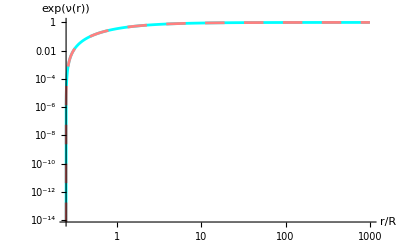

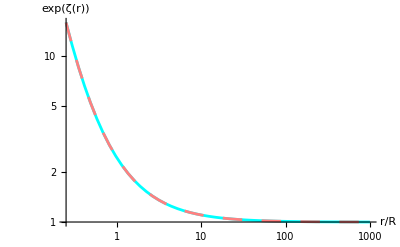

```mathematica
rparams={R->1,rinf->10^3};
nsol=NDSolve[{ttνζNoℱvto𝒥0ζSchw,ν[rinf]==νInf,ν'[rinf]==d1νInf,ν''[rinf]==d2νInf}/.rparams,ν,{r,R/4/.rparams,rinf/.rparams},PrecisionGoal->20,WorkingPrecision->50][[1]];

LogLogPlot[{E^ν[r]/.nsol,((1-R/(4r))/(1+R/(4r)))^2/.rparams},{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Cyan},{Dashing[Large],Thickness[0.005],Pink}},AxesLabel->{"r/R","exp(ν(r))"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]
LogLogPlot[{E^ζ[r]/.ζAnsatz/.a->4/.rparams,(1+R/(4r))^4/.rparams},{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Cyan},{Dashing[Large],Thickness[0.005],Pink}},AxesLabel->{"r/R","exp(ζ(r))"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]
```

The pink-dashed line shows the Schwarzschild solution. The value of the redshift function, near the (suspected) event horizon is...

```mathematica
(* E^ν[r] value near speculated horizon *)
E^ν[r]/.nsol/.r->(R/4/.rparams)
```

1.2597641800608990686259561756964846787×10^-22

This shows that the numerical solution can be practically viewed as the Schwarzschild black hole with the same parameters. However, it would be useful to quantify how much deviation there is from the Schwarzschild solution. In percent error, this is computed for ν(r) below...

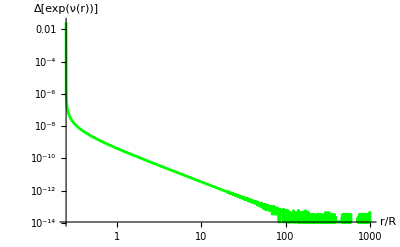

```mathematica
EνSchw=((1-R/(4r))/(1+R/(4r)))^2;
EζSchw=(1+R/(4r))^4;

LogLogPlot[{Abs[(E^ν[r]-EνSchw)/EνSchw]*100/.nsol/.rparams},{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Green}},AxesLabel->{"r/R","Δ[exp(ν(r))]"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]
```

What this reveals is that the numerically resolvable deviation can be found near the event horizon, as is expected in the strong gravity regime. The potential corresponding to this solution can also be obtained:

```mathematica
ℱvto𝒥0=ℱ[𝒴[r],0]==(ℱ[E^(-ζ[r])Φ'[r]^2,0]/.ℱfromθθvto/.ΦToΨ/.ΨrrConstraint/.𝒥->0//Simplify);
ℱof𝒴vto𝒥0=Derivative[1,0][ℱ][𝒴[r],0]==(Derivative[1,0][ℱ][E^(-ζ[r])Φ'[r]^2,0]/.ℱof𝒴fromSeqvto/.ΦToΨ/.ΨrrConstraint/.𝒥->0//Simplify);

ℱvto𝒥0
ℱof𝒴vto𝒥0
```

ℱ[𝒴 | r
 ,0]==1/(4 r^2 (-2+Κ) ν'[r]^2)ⅇ^(-ζ[r]) (r^2 ζ'[r]^4-4 r (-3+Κ) ν'[r]^3+r^2 ν'[r]^4+4 r ζ'[r]^3 (1+r ν'[r])-8 r ν'[r] (ζ''[r]+ν''[r])+4 r^2 (ζ''[r]+ν''[r])^2+2 ζ'[r]^2 (2+6 r ν'[r]+3 r^2 ν'[r]^2-2 r^2 ζ''[r]-2 r^2 ν''[r])+ν'[r]^2 (4-4 r^2 (-1+Κ) ζ''[r]-4 r^2 (-1+Κ) ν''[r])+4 ζ'[r] (-r (-5+Κ) ν'[r]^2+r^2 ν'[r]^3-2 r (ζ''[r]+ν''[r])-2 ν'[r] (-1+r^2 ζ''[r]+r^2 ν''[r])))

ℱ^(1,0)[𝒴 | r
 ,0]==((-2+Κ) (r ζ'[r]^2+2 ν'[r]+r ν'[r]^2+2 ζ'[r] (1+r ν'[r])-2 r (ζ''[r]+ν''[r])))/(r ζ'[r]^2+2 ν'[r]+r (-1+Κ) ν'[r]^2+2 ζ'[r] (1+r ν'[r])-2 r (ζ''[r]+ν''[r]))

The above expressions show that the potential (in other words, the model) depends on the coupling Κ unlike the metric functions. The radial profile of the potential function, the scalar field, as well as the scalar-vector-tensor coupling function 𝒴(r) can be shown to be...

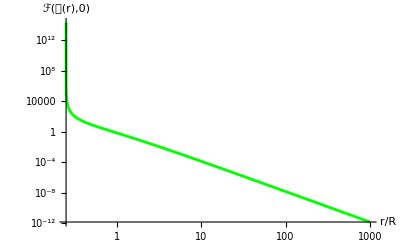

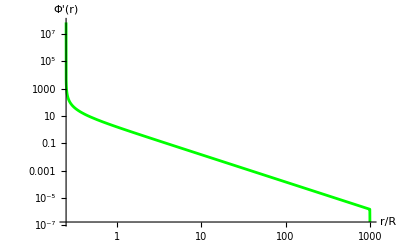

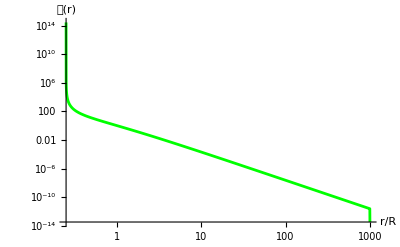

```mathematica
(* the SV potential *)
LogLogPlot[ℱvto𝒥0[[2]]/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Green}},AxesLabel->{"r/R","ℱ(𝒴(r),0)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]

(* the scalar hair *)
LogLogPlot[Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Green}},AxesLabel->{"r/R","Φ'(r)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]

(* the scalar-vector-tensor coupling 𝒴 *)
LogLogPlot[E^(-ζ[r])Ψ[r]^2/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Green}},AxesLabel->{"r/R","𝒴(r)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]
```

We can further explicitly construct the shape dependence of ℱ on 𝒴...

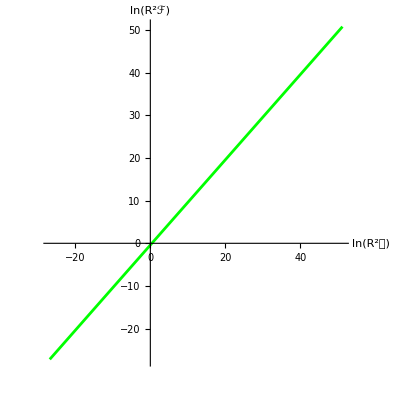

```mathematica
ParametricPlot[{Log[E^(-ζ[r])Ψ[r]^2/.ΨrrConstraint/.𝒥->0],Log[ℱvto𝒥0[[2]]]}/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Green}},AxesLabel->{"ln(R^2𝒴)","ln(R^2ℱ)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]]
```

Now, let’s relax the asymptotic condition by only keeping the leading order to be able to see a strong deviation from the Schwarzschild solution...

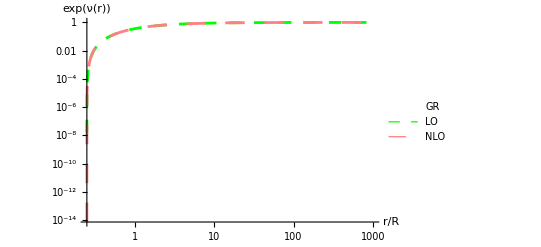

```mathematica
νInfLO=-R/rinf;
d1νInfLO=R/rinf^2;
d2νInfLO=-(2R)/rinf^3;

rparamsLO={R->1,rinf->10^3};
nsolLO=NDSolve[{ttνζNoℱvto𝒥0ζSchw,ν[rinf]==νInfLO,ν'[rinf]==d1νInfLO,ν''[rinf]==d2νInfLO}/.rparamsLO,ν,{r,R/4/.rparamsLO,rinf/.rparamsLO},PrecisionGoal->20,WorkingPrecision->50][[1]];

νinset=LogLogPlot[{Abs[(E^ν[r]-EνSchw)/EνSchw]*100/.nsolLO/.rparamsLO,Abs[(E^ν[r]-EνSchw)/EνSchw]*100/.nsol/.rparams},{r,R/4/.rparamsLO,rinf/.rparamsLO},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[Medium],Green},{Thickness[0.005],Dashing[Large],Pink}},AxesLabel->{"r/R","Δ[exp(ν(r))]"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]];
νplot=LogLogPlot[{((1-R/(4r))/(1+R/(4r)))^2/.rparamsLO,E^ν[r]/.nsolLO,E^ν[r]/.nsol},{r,R/4/.rparamsLO,rinf/.rparamsLO},PlotRange->All,PlotStyle->{{Thickness[0.005],White},{Dashing[Medium],Thickness[0.005],Green},{Dashing[Large],Thickness[0.005],Pink}},AxesLabel->{"r/R","exp(ν(r))"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"GR","LO","NLO"},Epilog->Inset[νinset,{Log[10^2/2],Log[10^-8]},Automatic,Scaled[0.7]]]
```

It is illustrative to compare the potentials corresponding to both solutions...

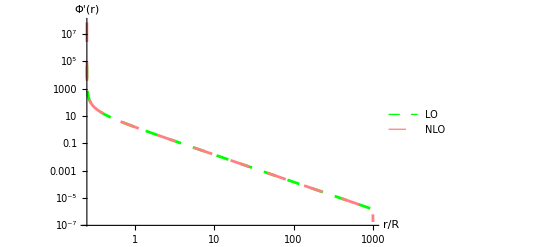

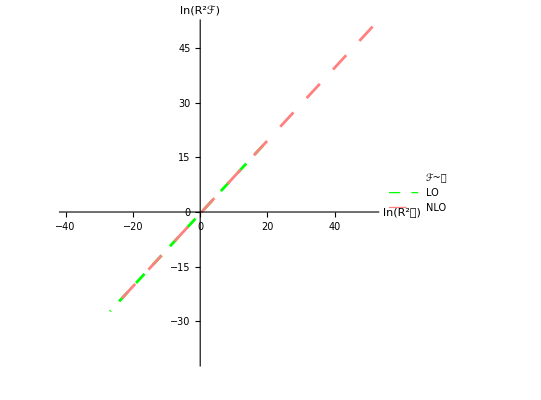

```mathematica
(* plots of the scalar hair *)
Φinset=LogLogPlot[Abs[((Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol)-(Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparamsLO/.nsolLO))/(Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol)]*100,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[None],Orange}},AxesLabel->{"r/R","ΔΦ'(r)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red]];

Φ1plot=LogLogPlot[Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[Large],Pink}},AxesLabel->{"r/R","Φ'(r)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"NLO"}];
Φ2plot=LogLogPlot[Ψ[r]/.ΨrrConstraint/.𝒥->0/.ζAnsatz/.a->4/.Κ->3/.rparamsLO/.nsolLO,{r,R/4/.rparamsLO,rinf/.rparamsLO},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[Medium],Green}},AxesLabel->{"r/R","Φ'(r)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"LO"}];

Show[Φ2plot,Φ1plot,PlotRange->All,Epilog->Inset[Φinset,{Log[2 10^2/3],Log[10^3]},Automatic,Scaled[0.65]],AxesOrigin->{Log[R/4/.rparams],Log[10^-7]}]

(* plots of the TEVES potential *)
pSchw=ParametricPlot[{Log[𝒴],Log[(2(Κ-2))/Κ 𝒴]}/.Κ->3,{𝒴,E^-40,E^50},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[None],White}},AxesLabel->{"ln(R^2𝒴)","ln(R^2ℱ)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"ℱ~𝒴"}];

p1=ParametricPlot[{Log[E^(-ζ[r])Ψ[r]^2/.ΨrrConstraint/.𝒥->0],Log[ℱvto𝒥0[[2]]]}/.ζAnsatz/.a->4/.Κ->3/.rparams/.nsol,{r,R/4/.rparams,rinf/.rparams},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[Large],Pink}},AxesLabel->{"ln(R^2𝒴)","ln(R^2ℱ)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"NLO"}];
p2=ParametricPlot[{Log[E^(-ζ[r])Ψ[r]^2/.ΨrrConstraint/.𝒥->0],Log[ℱvto𝒥0[[2]]]}/.ζAnsatz/.a->4/.Κ->3/.rparamsLO/.nsolLO,{r,R/4/.rparamsLO,rinf/.rparamsLO},PlotRange->All,PlotStyle->{{Thickness[0.005],Dashing[Medium],Green}},AxesLabel->{"ln(R^2𝒴)","ln(R^2ℱ)"},AxesStyle->Directive[Red],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red],PlotLegends->{"LO"}];

Show[pSchw,p2,p1,PlotRange->All]
```

We move to the general vector field case.

#### A general time-space vector field

We present a generalization of a hairy Schwarzschild black hole obtained using the designer approach in the previous section.

We focus on the linear potential...

```mathematica
ℱlin=ℱ->Function[{𝒴,𝒬},(2 (-2+Κ))/Κ 𝒴];

ℱ[𝒴,𝒬]==(ℱ[𝒴,𝒬]/.ℱlin)
```

ℱ[𝒴,𝒬]==(2 𝒴 (-2+Κ))/Κ

We then substitute the Schwarzschild solution into the field equations to see how we can proceed...

```mathematica
(* schwarzschild solution *)
$Assumptions=r>0&&R>0&&r≥R/4;
schw={ν->Function[r,Log[((1-R/(4r))/(1+R/(4r)))^2]],ζ->Function[r,Log[(1+R/(4r))^4]]};

(* metric field equation *)
EEvacIso[[1,1]]/.ℱlin/.schw//Simplify
EEvacIso[[1,2]]/.ℱlin/.schw//Simplify
EEvacIso[[2,2]]/.ℱlin/.schw//Simplify
EEvacIso[[3,3]]/.ℱlin/.schw//Simplify

(* scalar field equation *)
SqrtDetgIsoNoAngular=Simplify[SqrtDetgIso/Sin[θ],Assumptions->r≥0&&0≤θ≤Pi]/.√(x_^y_):>x^(y/2);
ShiftConstraint=SIso[[2]]==𝒥/SqrtDetgIsoNoAngular;ShiftConstraint/.ℱlin/.schw//Simplify

(* vector equation *)
VeqIso[[1]]/.ℱlin/.schw//Simplify
VeqIso[[2]]/.ℱlin/.schw//Simplify

(* constraint equation *)
ConstraintλIso/.ℱlin/.schw//Simplify
```

-(1024 r^2 R^2 (-4 r+R)^2)/(4 r+R)^8+(2048 r^2 R (-4 r+R)^2)/(4 r+R)^7-(1024 r^2 R (-4 r+R)^2 (8 r+R))/(4 r+R)^8-((-4 r+R)^2 σ[r])/(2 (4 r+R)^2)-1/2 𝒰[r]^2 σ[r]-(128 r^4 (-4 r+R)^2 𝒱[r]^2 σ[r])/(4 r+R)^6-(128 r^4 Κ 𝒰'[r]^2)/(4 r+R)^4+(1024 r^3 R 𝒰[r]^2 Φ'[r])/(4 r+R)^5-(1024 r^3 𝒰[r]^2 Φ'[r])/(4 r+R)^4-(512 r^3 R Κ 𝒰[r]^2 Φ'[r])/(4 r+R)^5+(512 r^3 Κ 𝒰[r]^2 Φ'[r])/(4 r+R)^4+(262144 r^7 R (-4 r+R)^2 𝒱[r]^2 Φ'[r])/(4 r+R)^11-(131072 r^7 R (-4 r+R)^2 Κ 𝒱[r]^2 Φ'[r])/(4 r+R)^11-(1024 r^4 𝒰[r] 𝒰'[r] Φ'[r])/(4 r+R)^4+(512 r^4 Κ 𝒰[r] 𝒰'[r] Φ'[r])/(4 r+R)^4+(131072 r^8 (-4 r+R)^2 𝒱[r] 𝒱'[r] Φ'[r])/(4 r+R)^10-(65536 r^8 (-4 r+R)^2 Κ 𝒱[r] 𝒱'[r] Φ'[r])/(4 r+R)^10-(256 r^4 (-4 r+R)^2 Φ'[r]^2)/(4 r+R)^6+(128 r^4 (-4 r+R)^2 Κ Φ'[r]^2)/(4 r+R)^6-(65536 r^8 (-4 r+R)^2 𝒱[r]^2 Φ'[r]^2)/(4 r+R)^10+(32768 r^8 (-4 r+R)^2 Κ 𝒱[r]^2 Φ'[r]^2)/(4 r+R)^10-(256 r^4 (-4 r+R)^2 (-2+Κ) ((4 r+R)^4+256 r^4 𝒱[r]^2) Φ'[r]^2)/((4 r+R)^10 Κ)-(512 r^4 𝒰[r]^2 Φ''[r])/(4 r+R)^4+(256 r^4 Κ 𝒰[r]^2 Φ''[r])/(4 r+R)^4

𝒰[r] 𝒱[r] (-σ[r]+(256 r^4 (-2+Κ) (32 r Κ Φ'[r]+(16 r^2-R^2) (-2+Κ) Φ'[r]^2+(16 r^2-R^2) Κ Φ''[r]))/((4 r-R) (4 r+R)^5 Κ))

-(((4 r+R)^6 𝒰[r]^2+(-4 r+R)^2 (-(4 r+R)^4+256 r^4 𝒱[r]^2)) σ[r])/(512 r^4 (-4 r+R)^2)+1/2 (((4 r+R)^2 Κ 𝒰'[r]^2)/(-4 r+R)^2+1/((-4 r+R)^3 (4 r+R)^5 Κ)(-2+Κ) (16 R (4 r+R)^6 Κ 𝒰[r]^2 Φ'[r]-(-4 r+R)^2 (-512 r^4 (16 r^2-R^2) Κ 𝒱[r] 𝒱'[r] Φ'[r]+(4 r-R) (4 r+R)^5 (-2+Κ) Φ'[r]^2+256 r^3 𝒱[r]^2 (4 (16 r^2-4 r R+R^2) Κ Φ'[r]+3 r (16 r^2-R^2) (-2+Κ) Φ'[r]^2+2 r (16 r^2-R^2) Κ Φ''[r]))))

-1/(512 r^2 (4 r-R)^3)((4 r-R) ((4 r+R)^6 𝒰[r]^2-(-4 r+R)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2)) σ[r]+1/((4 r+R)^5 Κ)256 r^4 ((4 r-R) (4 r+R)^7 Κ^2 𝒰'[r]^2+(-2+Κ) Φ'[r] (-16 R (4 r+R)^6 Κ 𝒰[r]^2+(4 r-R)^3 (-512 r^4 (4 r+R) Κ 𝒱[r] 𝒱'[r]+(4 r+R)^5 (-2+Κ) Φ'[r]+256 r^3 𝒱[r]^2 (-4 R Κ+r (4 r+R) (-2+Κ) Φ'[r])))))

1/((4 r-R) Κ)(-8 R (4 r+R)^6 (-2+Κ) Κ 𝒰[r]^2+(-4 r+R)^2 (-256 r^4 (16 r^2-R^2) (-2+Κ) Κ 𝒱[r] 𝒱'[r]+256 r^3 (4 r-R) (-2+Κ) 𝒱[r]^2 (-2 R Κ+r (4 r+R) (-2+Κ) Φ'[r])+(4 r+R)^4 (-8 𝒥 Κ+(16 r^2-R^2) (-2+Κ)^2 Φ'[r])))==0

1/((4 r-R) (4 r+R)^5)(-2 𝒰[r] ((4 r-R) (4 r+R)^5 σ[r]-4096 r^4 R (-2+Κ) Φ'[r])+512 r^4 Κ (16 (2 r-R) 𝒰'[r]+(16 r^2-R^2) 𝒰''[r]))

-2 𝒱[r] σ[r]+(512 r^4 (-2+Κ) 𝒱[r] (32 r Κ Φ'[r]+(16 r^2-R^2) (-2+Κ) Φ'[r]^2+(16 r^2-R^2) Κ Φ''[r]))/((4 r-R) (4 r+R)^5 Κ)

((4 r+R)^2 𝒰[r]^2)/(-4 r+R)^2==1+(256 r^4 𝒱[r]^2)/(4 r+R)^4

To obtain the solution (Φ,𝒰,𝒱) of this system, we start by first eliminating the multiplier using the time part of the vector field equation. The remaining equations then become...

```mathematica
σGenV=DSolve[VeqIso[[1]]==0/.ℱlin/.schw//Simplify,σ,r][[1]];

(* metric field equation *)
ttNoσ=EEvacIso[[1,1]]/.ℱlin/.schw/.σGenV//Simplify;
trNoσ=EEvacIso[[1,2]]/.ℱlin/.schw/.σGenV//Simplify;
rrNoσ=EEvacIso[[2,2]]/.ℱlin/.schw/.σGenV//Simplify;
θθNoσ=EEvacIso[[3,3]]/.ℱlin/.schw/.σGenV//Simplify;

(* scalar field equation *)
ShiftConstraintNoσ=ShiftConstraint/.ℱlin/.schw/.σGenV//Simplify;

(* vector equation *)
rvfeNoσ=VeqIso[[2]]/.ℱlin/.schw/.σGenV//Simplify;

(* constraint equation *)
ConstraintλIsoNoσ=ConstraintλIso/.ℱlin/.schw/.σGenV//Simplify;
```

The equations are a bit unwieldy and so we suppress them from appearing explicitly. Nonetheless, they can be handled efficiently by algebra packages. To obtain the scalar and vector hairs, we focus on the last three of these...

```mathematica
ShiftConstraintNoσ
rvfeNoσ
ConstraintλIsoNoσ
```

1/((4 r-R) Κ)(-8 R (4 r+R)^6 (-2+Κ) Κ 𝒰[r]^2+(-4 r+R)^2 (-256 r^4 (16 r^2-R^2) (-2+Κ) Κ 𝒱[r] 𝒱'[r]+256 r^3 (4 r-R) (-2+Κ) 𝒱[r]^2 (-2 R Κ+r (4 r+R) (-2+Κ) Φ'[r])+(4 r+R)^4 (-8 𝒥 Κ+(16 r^2-R^2) (-2+Κ)^2 Φ'[r])))==0

(512 r^4 𝒱[r] (16 (-2 r+R) Κ^2 𝒰'[r]+(-16 r^2+R^2) Κ^2 𝒰''[r]+(-2+Κ) 𝒰[r] (16 (2 r-R) Κ Φ'[r]+(16 r^2-R^2) (-2+Κ) Φ'[r]^2+(16 r^2-R^2) Κ Φ''[r])))/((4 r-R) (4 r+R)^5 Κ 𝒰[r])

((4 r+R)^2 𝒰[r]^2)/(-4 r+R)^2==1+(256 r^4 𝒱[r]^2)/(4 r+R)^4

Solving the time component 𝒰(r) of the vector field using the constraint, and then solving for the scalar field using the scalar constraint, we get...

```mathematica
𝒰GenV=DSolve[ConstraintλIsoNoσ,𝒰,r][[2]];

(* solving for the scalar, algebraically on its constraint surface *)
ΦtoΨ={Φ'[r]->Ψ[r],Φ''[r]->Ψ'[r]};
ΦGenV=DSolve[ShiftConstraintNoσ/.ΦtoΨ,Ψ,r][[1]];

𝒰[r]==(𝒰[r]/.𝒰GenV//FullSimplify)
Φ'[r]==(Ψ[r]/.ΦGenV/.𝒰GenV//FullSimplify)
```

𝒰[r]==((4 r-R) √((4 r+R)^4+256 r^4 𝒱[r]^2))/(4 r+R)^3

Φ'[r]==(8 Κ ((4 r+R)^4 (𝒥+R (-2+Κ))+32 r^3 (-2+Κ) 𝒱[r] (2 (8 r-R) R 𝒱[r]+r (16 r^2-R^2) 𝒱'[r])))/((4 r-R) (4 r+R) (-2+Κ)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2))

Substituting these into the metric field equations lead to...

```mathematica
ttNoσ/.ΦtoΨ/.ΦGenV/.𝒰GenV//FullSimplify
trNoσ/.ΦtoΨ/.ΦGenV/.𝒰GenV//FullSimplify
rrNoσ/.ΦtoΨ/.ΦGenV/.𝒰GenV//FullSimplify
θθNoσ/.ΦtoΨ/.ΦGenV/.𝒰GenV//FullSimplify
```

(8192 r^4 𝒥^2 Κ)/((4 r+R)^4 (-2+Κ)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2))

(16384 r^4 𝒥^2 Κ 𝒱[r])/((16 r^2-R^2) (-2+Κ)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2)^(3/2))

(32 (4 r+R)^2 𝒥^2 Κ ((4 r+R)^4+768 r^4 𝒱[r]^2))/((-4 r+R)^2 (-2+Κ)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2)^2)

-(32 r^2 (4 r+R)^2 𝒥^2 Κ)/((-4 r+R)^2 (-2+Κ)^2 ((4 r+R)^4+256 r^4 𝒱[r]^2))

We can thus see that in order for the solution (Φ(r),𝒰(r),𝒱(r)) to work, we must either have 𝒥=0 (zero shift charge) or K=0 (no vector kinetic term). However, K=0 also sets Φ'(r)=0, removing the scalar hair. The solution we seek is then comes from 𝒥=0 where the scalar field is given by...

```mathematica
Φ'[r]==(Ψ[r]/.ΦGenV/.𝒰GenV/.𝒥->0//FullSimplify)
```

Φ'[r]==(8 Κ (R (4 r+R)^4+32 r^3 𝒱[r] (2 (8 r-R) R 𝒱[r]+r (16 r^2-R^2) 𝒱'[r])))/((4 r-R) (4 r+R) (-2+Κ) ((4 r+R)^4+256 r^4 𝒱[r]^2))

Now, our final issue here is to alleviate the divergence of Φ'(r), if possible. This can be done by choosing 𝒱(r) appropriately. We illustrate this for one case:

```mathematica
CureSamp=R (4 r+R)^4+32 r^3 𝒱[r] (2 (8 r-R) R 𝒱[r]+r (16 r^2-R^2) 𝒱'[r])==γ(4r-R);
𝒱CureSamp=DSolve[CureSamp,𝒱,r];

(* just (+) branch, same cure for (-) branch *)
𝒱[r]==(Series[𝒱[r]/.𝒱CureSamp[[2]]//Simplify,{r,R/4,0}])
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

𝒱[r]==-(√(240 R^6-R^2 γ+61440 R^6 C[1]))/(2 (√15 R^2) (r-R/4))+(240 R^4-γ+61440 R^4 C[1])/(√15 R √(R^2 (240 R^4-γ+61440 R^4 C[1])))+O[r-R/4]^1

The spatial part of the vector inherited the singularity at r=R/4 (the event horizon). This can be removed by choosing the integration constant c_1 such that...

```mathematica
CureSampC1=Solve[15360 R^2-(64 γ)/R^2+3932160 R^2 C[1]==0,C[1]][[1]];CureSampC1
```

{C[1]→(-240 R^4+γ)/(61440 R^4)}

The scalar and vector hairs of the Schwarzschild black hole are then given by...

```mathematica
(* scalar hair *)
Φ'[r]==(Ψ[r]/.ΦGenV/.𝒰GenV/.𝒥->0/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify)

(* vector hair *)
𝒰[r]==(𝒰[r]/.𝒰GenV/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify)
𝒱[r]==(𝒱[r]/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify)
```

Φ'[r]==(1920 R^4 Κ)/((4 r-R) (4 r+R) (64 r^3+144 r^2 R+156 r R^2+111 R^3) (-2+Κ))

𝒰[r]==-((-4 r+R) √(((4 r-R) (64 r^3+144 r^2 R+156 r R^2+111 R^3) γ)/R^4))/(4 √15 (4 r+R)^3)

𝒱[r]==-(√(-16 R^4 (4 r+R)^4-1/15 (-4 r+R) (64 r^3+144 r^2 R+156 r R^2+111 R^3) γ))/(64 r^2 R^2)

By removing the horizon singularity of the vector, the singularity reappeared in the scalar field. The multiplier becomes...

```mathematica
σ[r]==(σ[r]/.σGenV/.ΦtoΨ/.ΦGenV/.𝒰GenV/.𝒥->0/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify)
```

σ[r]==-(5898240 r^4 R^4 (256 r^4+384 r^3 R+192 r^2 R^2-24 r R^3-173 R^4) Κ)/((-4 r+R)^2 (4 r+R)^6 (64 r^3+144 r^2 R+156 r R^2+111 R^3)^2)

To see that this solution is at least clear of problems at infinity, we take its asymptotic expansion far away from the hole:

```mathematica
Φ'[r]==Series[(Ψ[r]/.ΦGenV/.𝒰GenV/.𝒥->0/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify),{r,∞,5}]
𝒰[r]==Series[(𝒰[r]/.𝒰GenV/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify),{r,∞,4}]
𝒱[r]==Series[(𝒱[r]/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify),{r,∞,1}]
σ[r]==Series[(σ[r]/.σGenV/.ΦtoΨ/.ΦGenV/.𝒰GenV/.𝒥->0/.𝒱CureSamp[[2]]/.CureSampC1//FullSimplify),{r,∞,6}]
```

Φ'[r]==(15 R^4 Κ)/(8 (-2+Κ) r^5)+O[1/r]^6

𝒰[r]==(√γ)/(4 √15 R^2)-(√15 R^2 √γ)/(128 r^4)+O[1/r]^5

𝒱[r]==-(√(-240 R^4+γ))/(4 (√15 R^2))-((120 R^4-γ) √(-240 R^4+γ))/(4 (√15 R (240 R^4-γ)) r)+O[1/r]^2

σ[r]==-(45 (R^4 Κ))/(8 r^6)+O[1/r]^7

This is the end.